```mathematica
DumpSave[NotebookDirectory[]<>"curve.mx","Global`"]
```

{Global`}

```mathematica
Get[NotebookDirectory[]<>"curve.mx"]
```

## API:

```mathematica
combineblk[A_?MatrixQ,B_?MatrixQ,C_?MatrixQ,D_?MatrixQ]:=Block[{n=Length@A,upper,lower},upper=MapThread[Join,{A,B}];lower=MapThread[Join,{C,D}];Join[upper,lower]];H11=(η k^2 -μ)*IdentityMatrix[2]+V PauliMatrix[3]-α k PauliMatrix[2];H12=Δ IdentityMatrix[2];H22=-(η k^2 -μ)*IdentityMatrix[2]+V PauliMatrix[3]+α k PauliMatrix[2];H=combineblk[H11,H12,H12,H22];Hp1=Eigenvalues[H][[2]];
Hp2=Eigenvalues[H][[4]];
```

```mathematica
Hc[a_?NumberQ,μ0_?NumberQ,Δ0_?NumberQ,V0_?NumberQ,α0_?NumberQ,dim_?IntegerQ]:=Block[{t=25/a^2,μ=μ0,α=α0/(2a),Vz=V0,Δ=Δ0},KroneckerProduct[PauliMatrix[3],KroneckerProduct[PauliMatrix[0],-t*(SparseArray[{Band[{1,2}]->1,Band[{2,1}]->1},{dim,dim}])+(-μ+2*t)IdentityMatrix[dim,SparseArray]]+KroneckerProduct[PauliMatrix[2],I*α*(SparseArray[{Band[{1,2}]->-1,Band[{2,1}]->1},{dim,dim}])]]+KroneckerProduct[PauliMatrix[0],KroneckerProduct[PauliMatrix[3],Vz*IdentityMatrix[dim,SparseArray]]]+KroneckerProduct[PauliMatrix[1],KroneckerProduct[PauliMatrix[0],Δ*IdentityMatrix[dim,SparseArray]]]]
```

```mathematica
wfexp[a_,μ_,vz_,dim_,index_]:=Block[{(*testp,testn*)},testp=Transpose[Sort[Select[Transpose[Eigensystem[Hexp[a,μ,vz,dim],-30,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞,"Shift"->If[vz^2<μ^2+.2^2,sc2[μ,.2,vz],0]}]],#[[1]]>0&],#1[[1]]<#2[[1]]&][[1;;3]]];testn=Transpose[Sort[Select[Transpose[Eigensystem[Hexp[a,μ,vz,dim],-30,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞,"Shift"->If[vz^2<μ^2+.2^2,-sc2[μ,.2,vz],0]}]],#[[1]]<0&],#1[[1]]>#2[[1]]&][[1;;3]]];ListLinePlot[(Total[ArrayReshape[Abs[testp[[2,index]]]^2,{4,dim}]]+Total[ArrayReshape[Abs[testn[[2,index]]]^2,{4,dim}]])/2,DataRange->{0,dim*a(*/ξ0[μ,3,vz]*)},PlotLabel->ToString[vz],PlotRange->Full]]
```

```mathematica
kf[μ0_,Δ0_,B0_]:=Block[{Hf,ef,findm,slk,α0=5,η0=25},Hf=√(V^2+k^2 α^2+Δ^2+k^4 η^2-2 k^2 η μ+μ^2-2 √(V^2 Δ^2+k^4 V^2 η^2+k^6 α^2 η^2-2 k^2 V^2 η μ-2 k^4 α^2 η μ+V^2 μ^2+k^2 α^2 μ^2))/.{μ->μ0,Δ->Δ0,α->α0,η->η0};ef[V0_,k0_]:=Block[{V=V0,k=k0},Chop[Hf]]//Simplify;findm[B_]:=Block[{V=B,μ=μ0,Δ=Δ0,α=α0,η=η0,sl,n},sl=Solve[D[V^2+k^2 α^2+Δ^2+k^4 η^2-2 k^2 η μ+μ^2-2 √(V^2 Δ^2+k^4 V^2 η^2+k^6 α^2 η^2-2 k^2 V^2 η μ-2 k^4 α^2 η μ+V^2 μ^2+k^2 α^2 μ^2),k]==0,k];slk=Select[sl[[All,1,2]],#∈Reals&&#>0&];(ef[V,#]&/@slk);n=Flatten@Position[(ef[V,#]&/@slk),Quiet@Min[(ef[V,#]&/@slk)]];slk[[n]]];findm[B0][[1]]]
```

```mathematica
gap[μ0_?NumberQ,Δ0_?NumberQ,B0_?NumberQ,α0_?NumberQ]:=Block[{Hf,ef,sl,findm,α=α0,η=25,μ=μ0,Δ=Δ0,V=B0,rt},Hf=H;rt=Solve[D[Hp1^2,k]==0,k];sl=Select[rt[[All,1,2]],#∈Reals&];Min[(Hp1/.k->#&)/@sl]]
```

```mathematica
gapkf[μ0_,Δ0_,B0_]:=Block[{Hf,ef,sl,findm,α0=5,η0=25},Hf=Block[{μ=μ0,Δ=Δ0,α=α0,η=η0},H];ef[V0_,k0_]:=Block[{k=k0,V=V0},Transpose[Sort[Transpose[Eigensystem[Chop[Hf]]],#1[[1]]<#2[[1]]&]]];findm[B_]:=Block[{V=B,μ=μ0,Δ=Δ0,α=α0,η=η0},sl=Solve[D[V^2+k^2 α^2+Δ^2+k^4 η^2-2 k^2 η μ+μ^2-2 √(V^2 Δ^2+k^4 V^2 η^2+k^6 α^2 η^2-2 k^2 V^2 η μ-2 k^4 α^2 η μ+V^2 μ^2+k^2 α^2 μ^2),k]==0,k];sl=Select[sl[[All,1,2]],#∈Reals&&#>0&];Min[(ef[V,#][[1,3]]&/@sl)]];findm[B0]]
```

## Curve fit

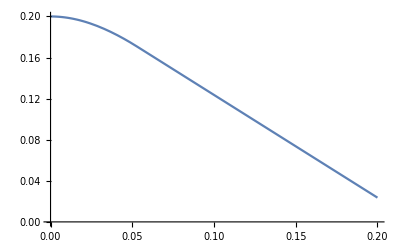
{2.76009,-Graphics-}

```mathematica
Plot[gap[.1,.2,x,5],{x,0,.2}]//AbsoluteTiming
```

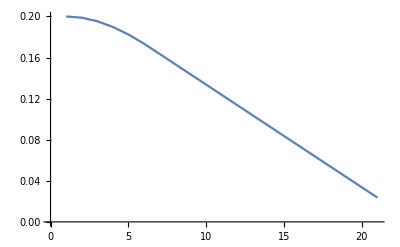
{0.363866,-Graphics-}

```mathematica
ListLinePlot@Table[gap[.1,.2,x,5],{x,0,.2,.01}]//AbsoluteTiming
```

```mathematica
Manipulate[ListLinePlot[Table[gap[μ,Δ,x,α],{x,0,.4,.01}],DataRange->{0,.2}],{μ,0.001,.2},{Δ,0.001,0.2},{α,1,5}]
```

```mathematica
Block[{μ=.1,Δ=.2,α=5,vzm,vzstep=0.01},vzm=√(μ^2+Δ^2);data=ParallelTable[Sort[Select[Eigenvalues[SparseArray@Hc[1,μ,Δ,vz,α,3000],-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞,"Shift"->.6*gap[μ,Δ,vz,α]}],#>0&]][[1]],{vz,0,vzm,vzstep}];(*scdata=Table[gap[μ,Δ,x,α],{x,0,vzm,vzstep}];*)dataint=Interpolation[Transpose@{Range[0,vzm,vzstep],data}];first=ParallelTable[D[dataint[x],x]/.x->x1,{x1,0,vzm,vzstep}];]
```

```mathematica
plotg[.1,.2,5];
```

{0.0031909,-0.0220648,-0.0470824,-0.0718621,-0.0964038,-0.120707,-0.144773,-0.168601,-0.192191,-0.215542,-0.238656,-0.261532,-0.284169,-0.306569,-0.328731,-0.350655,-0.37234,-0.393788,-0.414998,-0.43597,-0.456704,-0.477798,-0.498,-0.517927,-0.537579,-0.556957,-0.576059,-0.594886,-0.613439,-0.631716,-0.649718,-0.667159,-0.684638,-0.701859,-0.718824,-0.735531,-0.751981,-0.768173,-0.784109,-0.799787,-0.815208,-0.833982,-0.848554,-0.862644,-0.876255,-0.889385,-0.902034,-0.914203,-0.925891,-0.937098,-0.947825,-0.966172,-0.975187,-0.983219,-0.99027,-0.99634,-1.00143,-1.00553,-1.00866,-1.0108,-1.01196,-0.997339,-0.997911,-0.998416,-0.998856,-0.999229,-0.999536,-0.999777,-0.999953,-1.00006,-1.0001,-0.999025,-0.999034,-0.999043,-0.999051,-0.999058,-0.999064,-0.99907,-0.999075,-0.99908,-0.999084,-0.999084,-0.999087,-0.999089,-0.999091,-0.999092,-0.999093,-0.999094,-0.999094,-0.999093,-0.999092,-0.99909,-0.999088,-0.999086,-0.999083,-0.99908,-0.999076,-0.999072,-0.999068,-0.999063,-0.999058,-0.999052,-0.999046,-0.99904,-0.999033,-0.999025,-0.999018,-0.999009,-0.999001,-0.998991,-0.998982,-0.998973,-0.998963,-0.998952,-0.99894,-0.998928,-0.998915,-0.998902,-0.998888,-0.998874,-0.998862,-0.998847,-0.998831,-0.998814,-0.998797,-0.998779,-0.99876,-0.998741,-0.998721,-0.9987,-0.998678,-0.998661,-0.998638,-0.998613,-0.998588,-0.998562,-0.998534,-0.998506,-0.998477,-0.998446,-0.998415,-0.998392,-0.998358,-0.998322,-0.998285,-0.998246,-0.998206,-0.998164,-0.99812,-0.998075,-0.998046,-0.997998,-0.997946,-0.997893,-0.997836,-0.997777,-0.997716,-0.997651,-0.997585,-0.997515,-0.997443,-0.997404,-0.997323,-0.997238,-0.997148,-0.997053,-0.996954,-0.996849,-0.99674,-0.996626,-0.996507,-0.996466,-0.996331,-0.996185,-0.996029,-0.995864,-0.995688,-0.995503,-0.995308,-0.995102,-0.994888,-0.994895,-0.994639,-0.994358,-0.994053,-0.993724,-0.993371,-0.992994,-0.992592,-0.992166,-0.991716,-0.992121,-0.99154,-0.990882,-0.990144,-0.989328,-0.988433,-0.987459,-0.986407,-0.985276,-0.984067,-0.988565,-0.986661,-0.984321,-0.981544,-0.978331,-0.974681,-0.970594,-0.966071,-0.961111,-1.01175,-1.00423,-0.992922,-0.977811,-0.958902,-0.936194,-0.909687,-0.879382,-0.845278,-0.807376,-0.765675,-0.720176,-0.670878,-0.617782}

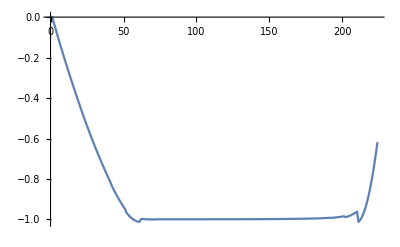

```mathematica
ListLinePlot[fd,PlotRange->Full]
```

```mathematica
plot[α0_?NumberQ]:=Block[{μ=.2,Δ=.2,α=α0,vzm,vzstep=0.01,p1,p2},vzm=√(μ^2+Δ^2);data=ParallelTable[Sort[Select[Re@Eigenvalues[SparseArray@Hc[1,μ,Δ,vz,α,30000],-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞,"Shift"->If[μ^2+Δ^2<vz^2,.5*gap[μ,Δ,vz,α],0]}],#>0&]][[1;;3]],{vz,0,vzm,vzstep}];scdata=Table[gap[μ,Δ,x,α],{x,0,vzm,vzstep}];dataint=Interpolation[Transpose@{Range[0,vzm,vzstep],data[[All,1]]}];secd=ParallelTable[D[dataint[x],{x,2}]/.x->x1,{x1,0,vzm,vzstep}];p1=ListLinePlot[Append[Transpose@data,scdata],DataRange->{0,√(μ^2+Δ^2)},PlotStyle->{Blue,Red,Yellow,Dashed},Frame->True,FrameLabel->{"Vz(meV)","E(meV)"},PlotLabel->"α="<>ToString[α/10]<>"(eV Å)",ImageSize->Large];p2=ListLinePlot[secd,DataRange->{0,√(μ^2+Δ^2)},PlotRange->Full,Frame->True,PlotLabel->"α="<>ToString[α/10]<>"(eV Å)",FrameLabel->{"Vz(meV)","E''(meV)"},ImageSize->Large,Axes->True,Epilog->{Line[{{-1,0},{1,0}}] }];{p1,p2}]
```

```mathematica
plotfd[μ0_?NumericQ,Δ0_?NumericQ,α0_?NumberQ]:=Block[{μ=μ0,Δ=Δ0,α=α0,vzm,vzstep=0.005},vzm=√(μ^2+Δ^2);data=ParallelTable[Sort[Select[Re@Eigenvalues[SparseArray@Hc[1,μ,Δ,vz,α,3000],-5,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞,"Shift"->If[μ^2+Δ^2<vz^2,.6*gap[μ,Δ,vz,α],0]}],#>0&]][[1]],{vz,0,vzm,vzstep}];(*scdata=Table[gap[μ,Δ,x,α],{x,0,vzm,vzstep}];*)dataint=Interpolation[Transpose@{Range[0,vzm,vzstep],data}];fd=ParallelTable[D[dataint[x],{x,1}]/.x->x1,{x1,0,vzm,vzstep}];p1=ListLinePlot[data,DataRange->{0,√(μ^2+Δ^2)},Frame->True,FrameLabel->{"Vz(meV)","E(meV)"},PlotLabel->"Spectrum, α="<>ToString[α/10.]<>"(eV Å)"<>"μ="<>ToString[μ]<>"meV, Δ="<>ToString[Δ]<>"meV",ImageSize->Large];p2=ListLinePlot[Abs@fd,DataRange->{0,√(μ^2+Δ^2)},Frame->True,PlotLabel->"g, α="<>ToString[α/10.]<>"(eV Å)"<>"μ="<>ToString[μ]<>"meV, Δ="<>ToString[Δ]<>"meV",PlotRange->{0,1},FrameLabel->{"Vz(meV)","g"},ImageSize->Large,Axes->True,Epilog->{Line[{{-1,0},{1,0}}] ,Line[{{-1,1},{1,1}}]}];{p1,p2}]
```

```mathematica
plottemp[α0_?NumberQ]:=Block[{μ=.2,Δ=1.1,α=α0,vzm,vzstep=0.005,p1,p2,t=25},vzm=√(μ^2+Δ^2);data=ParallelTable[PrintTemporary[vz];Sort[Select[Re[If[vz<abs,Eigenvalues[SparseArray@Hc[1,μ,Δ,vz,α,3000],-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞,"Shift"->.5*gap[μ,Δ,vz,α]}],Eigenvalues[SparseArray@Hc[1,μ,Δ,vz,α,30000],-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞,"Shift"->.95*gap[μ,Δ,vz,α]}]]],#>0&]][[1;;3]],{vz,0,vzm,vzstep}];scdata=Table[gap[μ,Δ,x,α],{x,0,vzm,vzstep}];dataint=Interpolation[Transpose@{Range[0,vzm,vzstep],data[[All,1]]}];secd=ParallelTable[D[dataint[x],{x,2}]/.x->x1,{x1,0,vzm,vzstep}];p1=ListLinePlot[Append[Transpose@data,scdata],DataRange->{0,√(μ^2+Δ^2)},PlotStyle->{Blue,Red,Yellow,Dashed},Frame->True,FrameLabel->{"Vz(meV)","E(meV)"},PlotLabel->"α="<>ToString[α/10.]<>"(eV Å)",ImageSize->Large];p2=ListLinePlot[secd,DataRange->{0,√(μ^2+Δ^2)},Frame->True,PlotLabel->"α="<>ToString[α/10.]<>"(eV Å)",FrameLabel->{"Vz(meV)","E''(meV)"},ImageSize->Large,Axes->True,PlotRange->Automatic,Epilog->{Line[{{-1,0},{1,0}}] }];{p1,p2}]
```

```mathematica
plotmu[μ0_]:=Block[{μ=μ0,Δ=.2,α=2,vzm,vzstep=0.005,p1,p2,t=25},vzm=√(μ^2+Δ^2);data=ParallelTable[PrintTemporary[vz];Sort[Select[Re[If[vz<abs,Eigenvalues[SparseArray@Hc[1,μ,Δ,vz,α,3000],-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞,"Shift"->.6*gap[μ,Δ,vz,α]}],Eigenvalues[SparseArray@Hc[1,μ,Δ,vz,α,3000],-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞,"Shift"->.95*gap[μ,Δ,vz,α]}]]],#>0&]][[1;;3]],{vz,0,vzm,vzstep}];scdata=Table[gap[μ,Δ,x,α],{x,0,vzm,vzstep}];dataint=Interpolation[Transpose@{Range[0,vzm,vzstep],data[[All,1]]}];secd=ParallelTable[D[dataint[x],{x,2}]/.x->x1,{x1,0,vzm,vzstep}];p1=ListLinePlot[Append[Transpose@data,scdata],DataRange->{0,√(μ^2+Δ^2)},PlotStyle->{Blue,Red,Yellow,Dashed},Frame->True,FrameLabel->{"Vz(meV)","E(meV)"},PlotLabel->"α="<>ToString[α/10.]<>"(eVÅ)"<>" μ="<>ToString[μ*1.]<>"(meV)",ImageSize->Large];p2=ListLinePlot[secd,DataRange->{0,√(μ^2+Δ^2)},Frame->True,PlotLabel->"α="<>ToString[α/10.]<>"(eVÅ)"<>" μ="<>ToString[μ*1.]<>"(meV)",FrameLabel->{"Vz(meV)","E''(meV)"},ImageSize->Large,Axes->True,PlotRange->Automatic,Epilog->{Line[{{-1,0},{1,0}}] }];{p1,p2}]
```

```mathematica
plotg[μ0_?NumericQ,Δ0_?NumericQ,α0_?NumberQ]:=Block[{μ=μ0,Δ=Δ0,α=α0,vzm,vzstep=0.01(*,data,scdata,dataint,secd*)},vzm=√(μ^2+Δ^2);data=ParallelTable[Sort[Select[Chop@Eigenvalues[SparseArray@Hc[1,μ,Δ,vz,α,3000],-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞,"Shift"->If[μ^2+Δ^2<vz^2,.6*gap[μ,Δ,vz,α],0]}],#>0&]][[1]],{vz,0,vzm*1.05,vzstep}];dataint=Interpolation[Transpose@{Range[0,vzm*1.05,vzstep],data}];fd=ParallelTable[D[dataint[x],x]/.x->x1,{x1,0,vzm,vzstep/10}]]
```

```mathematica
plot2d[μ0_?NumericQ,Δ0_?NumericQ,α0_?NumberQ]:=Block[{μ=μ0,Δ=Δ0,α=α0,vzm,vzstep=0.01(*,data,scdata,dataint,secd*)},vzm=√(μ^2+Δ^2);data=ParallelTable[Sort[Select[Chop@Eigenvalues[SparseArray@Hc[1,μ,Δ,vz,α,5000],-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞,"Shift"->If[μ^2+Δ^2<vz^2,.6*gap[μ,Δ,vz,α],0]}],#>0&]][[1;;3]],{vz,0,vzm*1.05,vzstep}];dataint=Interpolation[Transpose@{Range[0,vzm*1.05,vzstep],data[[All,1]]}];secd=ParallelTable[D[dataint[x],{x,2}]/.x->x1,{x1,0,vzm,vzstep/10}]]
```

```mathematica
maxsd[μ0_?NumericQ,Δ0_?NumericQ,α0_?NumberQ]:=Block[{μ=μ0,Δ=Δ0,α=α0,vzm,vzstep=0.01(*,data,scdata,dataint,secd*),},vzm=abs/.{t->25,Δ->Δ0,μ->μ0,α->α0};data=ParallelTable[Sort[Select[Chop@Eigenvalues[SparseArray@Hc[1,μ,Δ,vz,α,3000],-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞,"Shift"->If[μ^2+Δ^2<vz^2,.5*gap[μ,Δ,vz,α],0]}],#>0&]][[1;;3]],{vz,0,vzm,vzstep}];dataint=Interpolation[Transpose@{Range[0,vzm,vzstep],data[[All,1]]}];Maximize[{dataint''[x],0<x<vzm},x][[1]]]
```

```mathematica
maxsd[.2,.2,2.03]//AbsoluteTiming
```

{45.2277,0.00656096}

```mathematica
maxsd[.2,.2,2.03]//AbsoluteTiming
```

{35.719,Null}

```mathematica
Block[{start=0.,end=5.,current,val},current=(start+end)/2;val=maxsd[.2,.2,current];While[Abs[val]>1*^-3,If[val>0,start=current,end=current];current=(start+end)/2;val=maxsd[.2,.2,current];];current]//AbsoluteTiming
```

{136.291,2.04956}

```mathematica
maxα[μ0_,Δ0_]:=maxα[μ0,Δ0]=Block[{start=0.,end=5.,current,val,μ=μ0,Δ=Δ0},current=(start+end)/2;val=maxsd[μ,Δ,current];While[Abs[val]>1*^-3,If[val>0,start=current,end=current];current=(start+end)/2;val=maxsd[μ,Δ,current];];current]
```

```mathematica
Clear[maxα2]
```

```mathematica
maxα2[μ0_,Δ0_]:=maxα2[μ0,Δ0]=Block[{start=0.,end=5.,current,val,μ=μ0,Δ=Δ0},current=(start+end)/2;val=maxsd[μ,Δ,current];While[Abs[val]>1*^-3,If[val>0,start=current,end=current];current=(start+end)/2;val=maxsd[μ,Δ,current];];current]
```

```mathematica
maxα3[μ0_,Δ0_]:=maxα3[μ0,Δ0]=Block[{start=0.,end=5.,current,val,μ=μ0,Δ=Δ0},current=(start+end)/2;val=maxsd[μ,Δ,current];While[Abs[val]>1*^-3,If[val>0,start=current,end=current];current=(start+end)/2;val=maxsd[μ,Δ,current];];current]
```

```mathematica
maxα4[μ0_,Δ0_]:=maxα4[μ0,Δ0]=Block[{start=0.,end=5.,current,val,μ=μ0,Δ=Δ0},current=(start+end)/2;val=maxsd[μ,Δ,current];While[Abs[val]>1*^-3,If[val>0,start=current,end=current];current=(start+end)/2;val=maxsd[μ,Δ,current];];current]
```

```mathematica
maxα[.2,.2]//AbsoluteTiming
```

{2.1157×10^-6,2.04956}

```mathematica
Clear[]
```

```mathematica
maxmu[α0_,Δ0_]:=maxmu[α0,Δ0]=Block[{start=0.1,end=0.4,current,val,α=2,Δ=Δ0},current=(start+end)/2;val=maxsd[current,Δ,α];While[Abs[val]>1*^-3,If[val<0,start=current,end=current];current=(start+end)/2;val=maxsd[current,Δ,α];Print[{current,val}]];current]
```

```mathematica
maxmu[2,.2]
```

{0.175,-0.167671}

{0.2125,0.229331}

{0.19375,0.0442712}

{0.184375,-0.0657337}

{0.189062,-0.00723489}

{0.191406,0.0195024}

{0.190234,0.00638773}

{0.189648,-0.00035907}

0.189648

```mathematica
maxsd[0.18964843749999996,.2,2]
```

-0.00035907

```mathematica
plot2d[.1,.2,1]//AbsoluteTiming
```

{16.4177,{-67.9472,-64.9139,-61.8806,-58.8474,-55.8141,-52.7808,-49.7475,-46.7143,-43.681,-40.6477,-37.6144,-34.5812,-31.5479,-28.5146,-25.4813,-22.4481,-19.4148,-16.3815,-13.3482,-10.315,-7.28168,-6.75702,-6.23237,-5.70772,-5.18307,-4.65841,-4.13376,-3.60911,-3.08445,-2.5598,-2.03515,-1.89715,-1.75916,-1.62116,-1.48317,-1.34517,-1.20718,-1.06919,-0.931191,-0.793197,-0.655202,-0.601933,-0.548663,-0.495394,-0.442124,-0.388854,-0.335585,-0.282315,-0.229046,-0.175776,-0.122507,-0.0954653,-0.0684239,-0.0413826,-0.0143412,0.0127002,0.0397415,0.0667829,0.0938242,0.120866,0.147907,0.165051,0.182195,0.199339,0.216484,0.233628,0.250772,0.267916,0.28506,0.302205,0.319349,0.332384,0.34542,0.358455,0.371491,0.384526,0.397562,0.410597,0.423633,0.436668,0.449704,0.461025,0.472346,0.483667,0.494988,0.506309,0.51763,0.528951,0.540272,0.551593,0.562914,0.573566,0.584218,0.59487,0.605522,0.616174,0.626826,0.637478,0.64813,0.658782,0.669434,0.679761,0.690088,0.700415,0.710741,0.721068,0.731395,0.741722,0.752049,0.762376,0.772703,0.782492,0.792281,0.80207,0.81186,0.821649,0.831438,0.841227,0.851016,0.860806,0.870595,0.878937,0.887279,0.895621,0.903963,0.912305,0.920648,0.92899,0.937332,0.945674,0.954016,0.95885,0.963685,0.968519,0.973353,0.978188,0.983022,0.987856,0.992691,0.997525,1.00236,0.999451,0.996544,0.993636,0.990728,0.987821,0.984913,0.982005,0.979098,0.97619,0.973282,0.953885,0.934487,0.915089,0.895692,0.876294,0.856897,0.837499,0.818101,0.798704,0.779306,0.724127,0.668948,0.613769,0.558589,0.50341,0.448231,0.393052,0.337872,0.282693,0.227514,0.0877903,-0.0519335,-0.191657,-0.331381,-0.471105,-0.610829,-0.750552,-0.890276,-1.03,-1.16972,-1.55433,-1.93894,-2.32355,-2.70816,-3.09277,-3.47738,-3.86199,-4.2466,-4.6312,-5.01581,-5.24626,-5.47671,-5.70715,-5.9376,-6.16804,-6.39849,-6.62894,-6.85938,-7.08983,-7.32028,-6.54903,-5.77779,-5.00655,-4.23531,-3.46406,-2.69282,-1.92158,-1.15034,-0.379095,0.392147,6.58696,12.7818,18.9766,25.1714,31.3662,37.561,43.7558,49.9507,56.1455,62.3403,68.5351,74.7299,80.9247}}

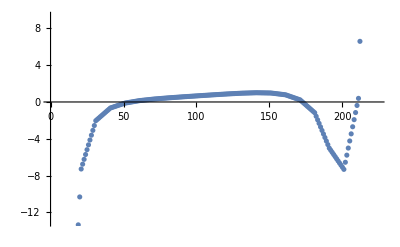

```mathematica
ListPlot[Out[556][[2]]]
```

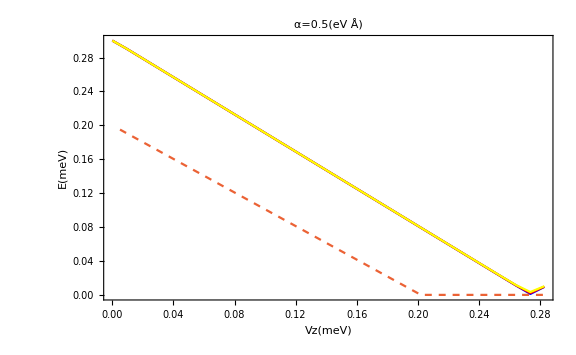

```mathematica
ListLinePlot[Append[Transpose@data,scdata],DataRange->{0,√(.2^2+.2^2)},PlotStyle->{Blue,Red,Yellow,Dashed},Frame->True,FrameLabel->{"Vz(meV)","E(meV)"},PlotLabel->"α="<>ToString[5/10.]<>"(eV Å)",ImageSize->Large]
```

```mathematica
listp={{.1,.2,2},{.2,.2,2},{.3,.2,2},{.4,.2,2},{.2,.2,0.001},{.2,.2,1},{.2,.2,3},{.2,.2,5},{.2,.2,10}};
```

```mathematica
Dynamic[ii]
```

```mathematica
plotfd[.2,.2,5]
```

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Mathematica\11.2\WolframKernel" -noicon -subkernel -noinit -nopaclet -wstp,3067,17].

Kernels::rdead: Subkernel connected through KernelObject[7,local] appears dead.

LaunchKernels::clone: Kernel KernelObject[7,local,<defunct>] resurrected as KernelObject[10,local].

$Aborted

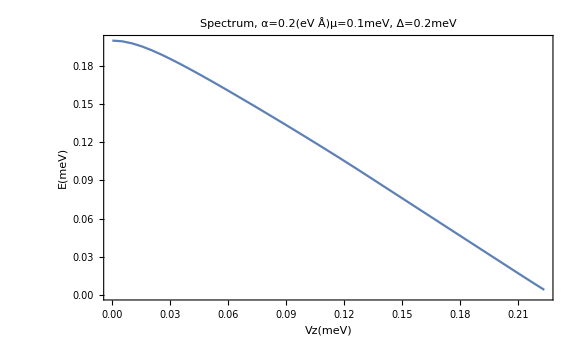
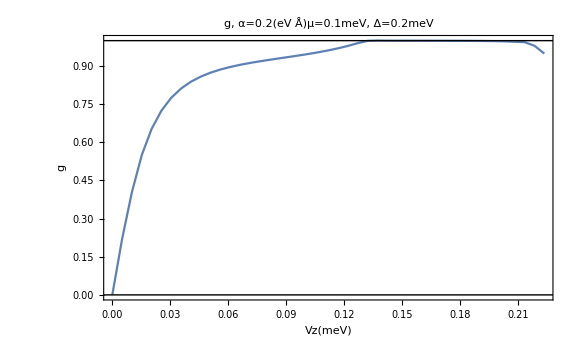
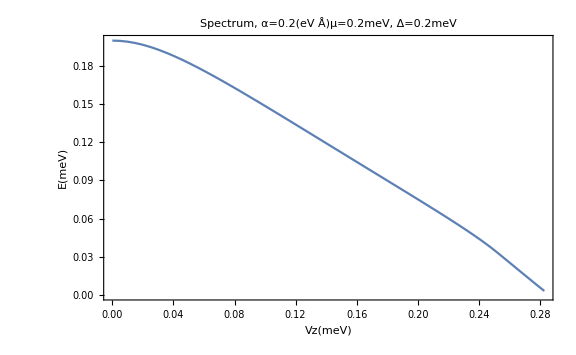
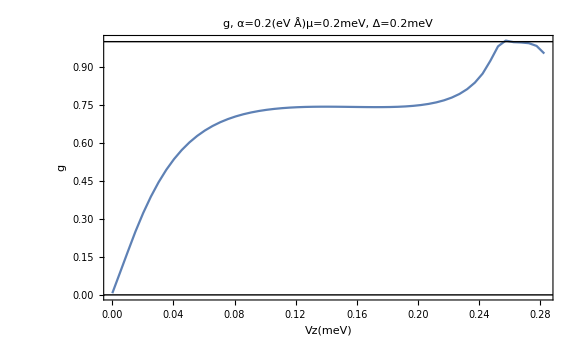
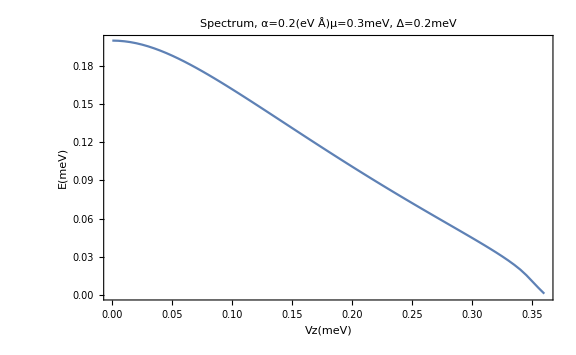
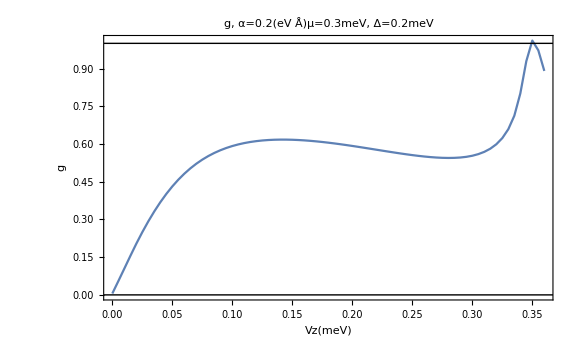
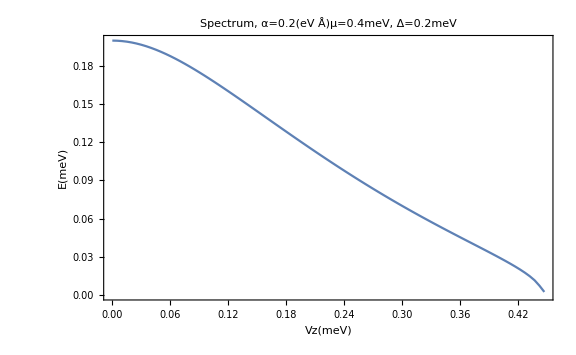
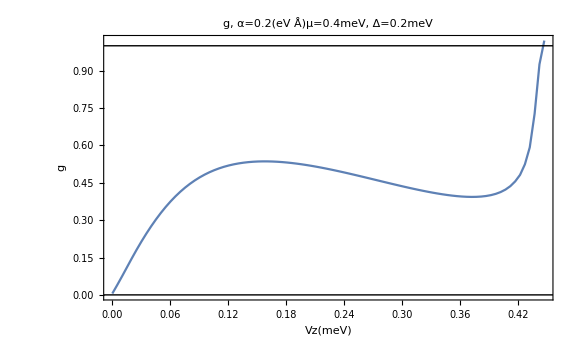

```mathematica
pl=Table[plotfd@@ii,{ii,listp}]
```

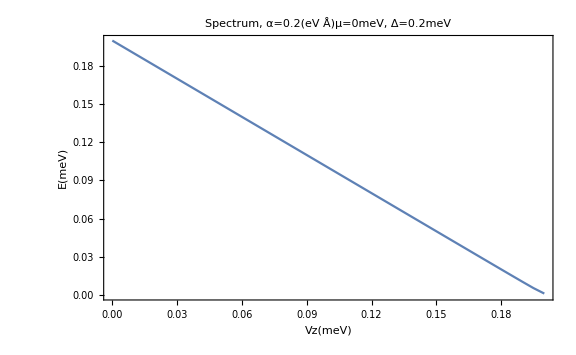
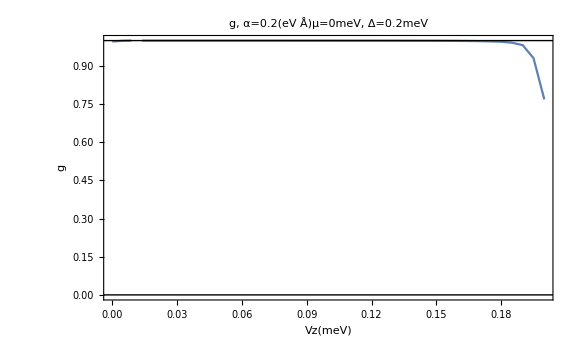

```mathematica
pl2=plotfd[0,.2,2]
```

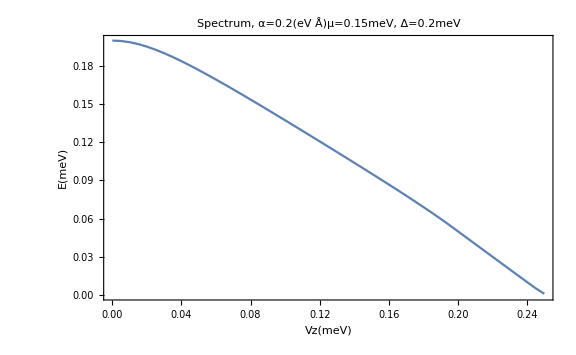
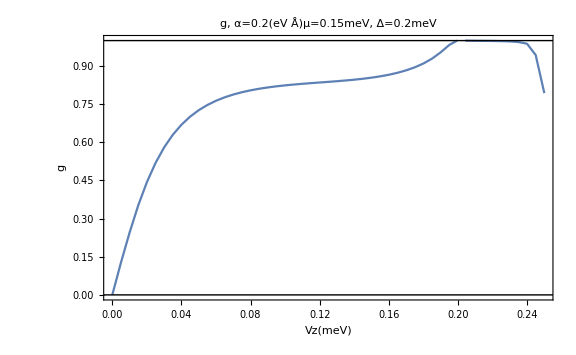

```mathematica
plotfd[.15,.2,2]
```

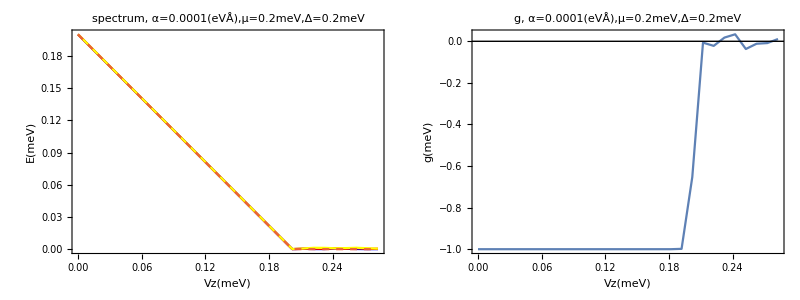

```mathematica
Grid[{{p1/.(PlotLabel->_)->PlotLabel->"spectrum, α=0.0001(eVÅ),μ=0.2meV,Δ=0.2meV" ,p2/.{(PlotLabel->_)->(PlotLabel->"g, α=0.0001(eVÅ),μ=0.2meV,Δ=0.2meV"),(FrameLabel->_)->FrameLabel-> {"Vz(meV)","g(meV)"}}}}]
```

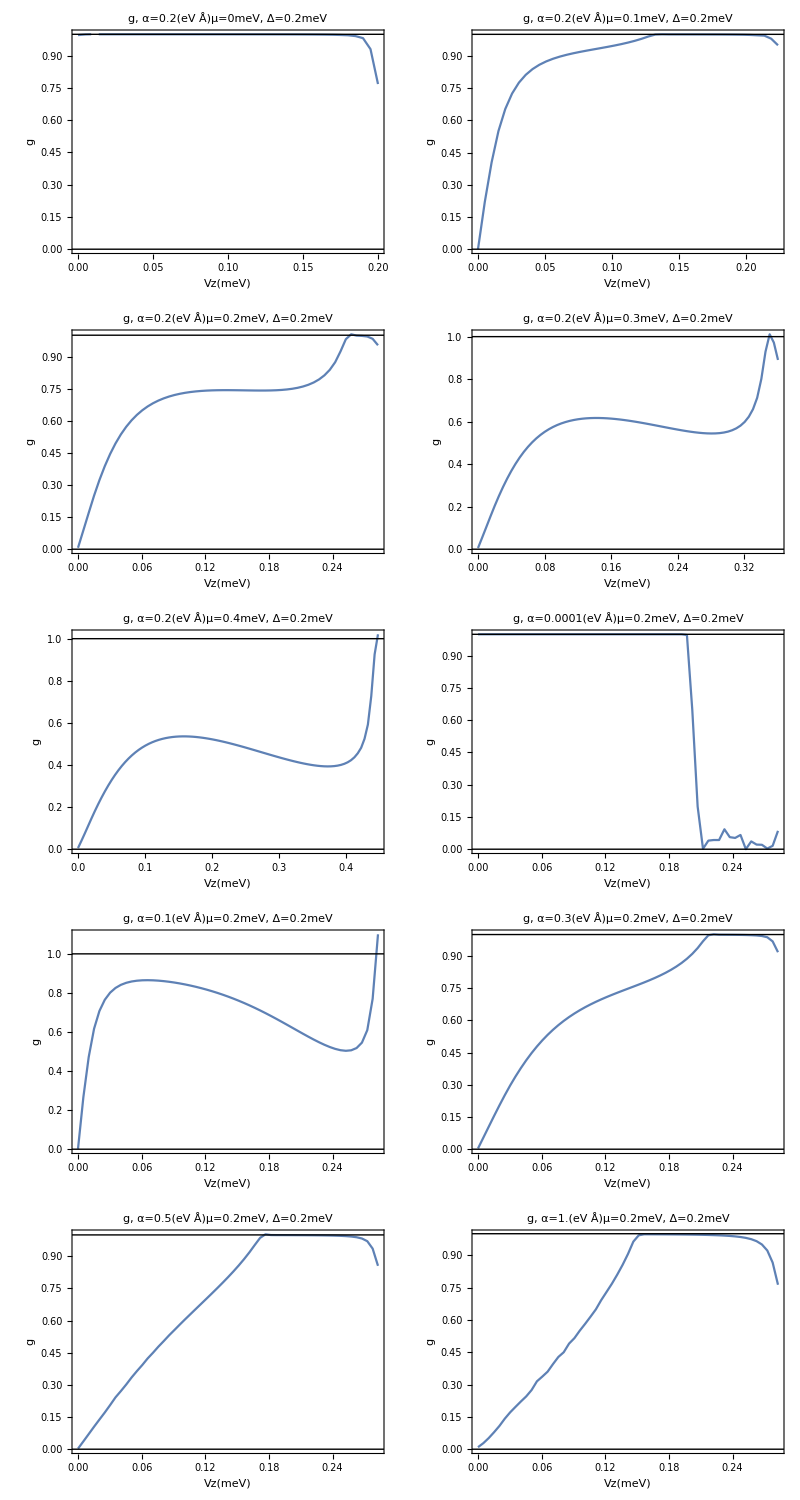

```mathematica
Grid@Partition[Prepend[pl,pl2][[All,2]],2]
```

```mathematica
ff=x^2+y^2-1
```

-1+x^2+y^2

```mathematica
D[√(1-x^2),{x,2}]*(D[ff,{y,2}]+D[ff,{y,1}])+D[√(1-x^2),x](2*D[ff,x,y])+D[ff,{x,2}]+D[ff,x]/.{y->√(1-x^2)}
```

2+2 x+(-x^2/((1-x^2)^(3/2))-1/(√(1-x^2))) (2+2 √(1-x^2))

```mathematica
2*D[ff,x,y]*D[√(1-x^2),x]+D[ff,{y,2}](D[ff,y])^2+D[ff,y]D[√(1-x^2),{x,2}]+D[ff,{x,2}]/.y->√(1-x^2)
```

2+8 (1-x^2)+2 √(1-x^2) (-x^2/((1-x^2)^(3/2))-1/(√(1-x^2)))

```mathematica
plotmu[.1]
```

```mathematica
data
```

{{0.3,0.300006,0.300007},{0.290667,0.290669,0.290672},{0.280667,0.28067,0.280675},{0.270667,0.270671,0.270676},{0.260667,0.260671,0.260678},{0.250667,0.250672,0.250679},{0.240668,0.240672,0.24068},{0.230668,0.230673,0.230682},{0.220668,0.220674,0.220683},{0.210668,0.210674,0.210685},{0.200668,0.200675,0.200687},{0.190668,0.190676,0.190689},{0.180669,0.180677,0.180691},{0.170669,0.170678,0.170694},{0.160669,0.160679,0.160696},{0.15067,0.150681,0.1507},{0.14067,0.140682,0.140703},{0.130671,0.130684,0.130707},{0.120671,0.120686,0.120712},{0.110672,0.110689,0.110718},{0.100672,0.100692,0.100724},{0.0906733,0.0906955,0.0907325},{0.0806744,0.0807,0.0807427},{0.0706759,0.0707058,0.0707557},{0.0606778,0.0607135,0.060773},{0.0506805,0.0507241,0.0507969},{0.0406844,0.0407399,0.0408323},{0.0306909,0.0307657,0.03089},{0.0207033,0.0208152,0.0210003},{0.0107372,0.0109486,0.0112931},{0.00112701,0.00217757,0.0033894},{0.0094343,0.00972805,0.0101968}}

```mathematica
dataint
```

InterpolatingFunction[…]

```mathematica
secd
```

{2 (-1.5 (66.6667 (-1.-100. (0.190012-Re[]))-200. (100. (0.190012-Re[])+200. (-0.195012+Re[])))+200. (100. (0.190012-Re[])+200. (-0.195012+Re[]))),2 (0.+200. (100. (0.190012-Re[])+200. (-0.195012+Re[]))),2 (-2.87759×10^-8-8.67362×10^-17 (2.87759×10^-8-200. (1.-66.6667 (-0.185012+Re[])))),-8.6708×10^-9,3.87246×10^-9,8.85056×10^-9,1.30032×10^-8,1.49678×10^-8,1.74083×10^-8,1.97811×10^-8,2.2484×10^-8,2.40985×10^-8,2.82776×10^-8,3.1054×10^-8,3.45663×10^-8,4.00563×10^-8,4.42957×10^-8,5.03797×10^-8,5.85027×10^-8,6.63219×10^-8,7.78772×10^-8,8.95883×10^-8,1.06331×10^-7,1.26232×10^-7,1.50352×10^-7,1.83552×10^-7,2.25613×10^-7,2.8144×10^-7,3.57568×10^-7,4.65273×10^-7,6.18976×10^-7,8.49816×10^-7,1.21144×10^-6,1.81396×10^-6,2.89263×10^-6,5.04385×10^-6,0.0000100313,0.0000248619,0.0000976794,0.05458,208.01,-2.8915,-14.2241,10.1884,17.1885,-37.883,21.8336,16.0097,-31.241,14.4252,-11.6587,14.5913,-7.60076,1.0857,7.62456,-10.9533,-29.5312}

```mathematica
secd=ParallelTable[D[dataint[x],{x,2}]/.x->x1,{x1,0,√(.1^2+.2^2),0.005}]
```

{-13.3238,-9.99319,-6.66256,-3.33192,-0.00128334,-0.000771387,-0.000259434,-0.000152365,-0.0000452963,-4.98038×10^-6,0.0000353355,0.0000571646,0.0000789938,0.0000946801,0.000110366,0.000124276,0.000138186,0.000152344,0.000166502,0.000182161,0.00019782,0.000216027,0.000234233,0.000256092,0.000277951,0.000304815,0.000331679,0.000365343,0.000399007,0.000441969,0.000484932,0.000540796,0.00059666,0.000670782,0.000744905,0.000845509,0.000946114,0.00108627,0.00122643,0.00142777,0.00162911,0.00192918,0.00222925,0.00269707,0.00316489}

```mathematica
abs/.{t->25,α->2,μ->.1,Δ->.2}
```

0.114556

```mathematica
plottemp[2.1875]
```

0.35

0.

0.05

0.1

0.15

0.2

0.25

0.3

0.155

0.205

0.055

0.255

0.305

$Aborted

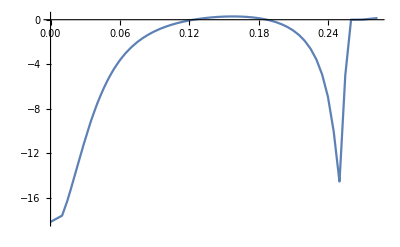

```mathematica
Plot[dataint''[x],{x,0,.2 √2}]
```

```mathematica
Maximize[{dataint''[x],0<x<.2 √2},{x}]
```

{0.291531,{x→0.16}}

```mathematica
dataint''[0.159]
```

0.291402

```mathematica
gap[.2,.2,.1,5]
```

0.16809

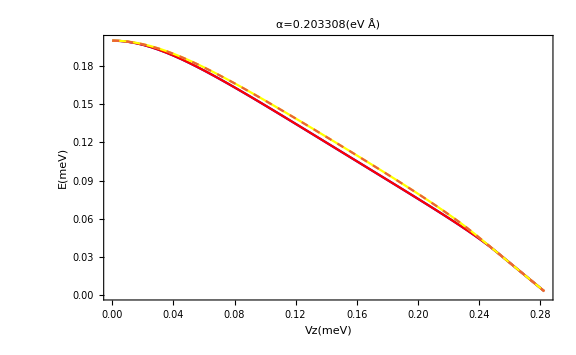
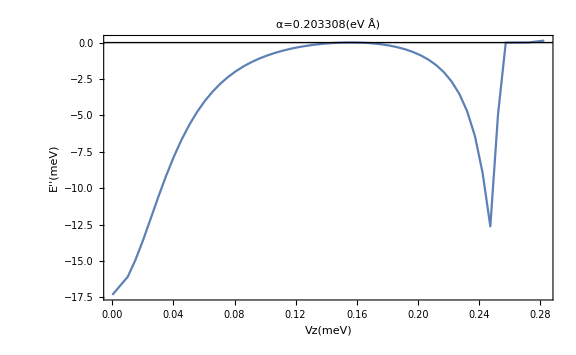

```mathematica
plottemp[2.03308105]
```

```mathematica
gapdata=ParallelTable[gap[.2,.2,vx,1.9],{vx,0,√(.2^2+.2^2),√(.2^2+.2^2)/1000}];
```

Min::nord: Invalid comparison with 0.+5.26836×10^-9 ⅈ attempted.

```mathematica
gapfit=Interpolation[Transpose@{Range[0,√(.2^2+.2^2),√(.2^2+.2^2)/1000],gapdata}]
```

InterpolatingFunction[…]

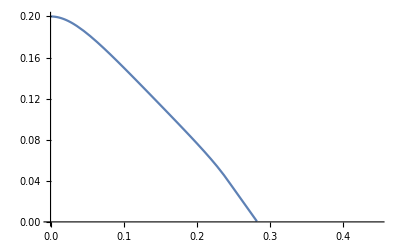

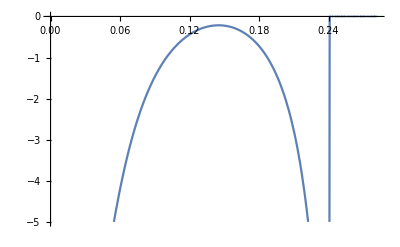

```mathematica
Plot[gapfit[x],{x,0,√(.2^2+.4^2)}]
```

```mathematica
Maximize[{gapfit''[x],0<x<.1},{x}]
```

{-Experimental`NumericalFunction[{x},-InterpolatingFunction[…][x],-NumericalFunctionData-][{0.0630621}],{x→0.0630621}}

```mathematica
abs/.{t->25,Δ->.2,μ->.2,α->2}
```

0.237168

```mathematica
plot2d[.4,.2,1]
```

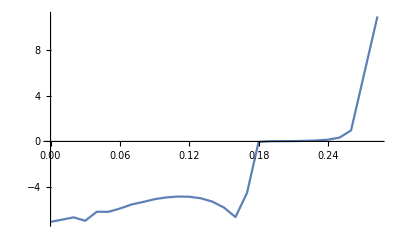

```mathematica
Plot[dataint''[x],{x,0,√(.2^2+.2^2)},PlotRange->Full]
```

```mathematica
abs/.{t->25,Δ->.2,μ->.2,α->5}
```

0.168657

```mathematica
Maximize[{dataint''[x],0<x<abs/.{t->25,Δ->.2,μ->.2,α->5}},x]
```

{-4.82542,{x→0.11}}

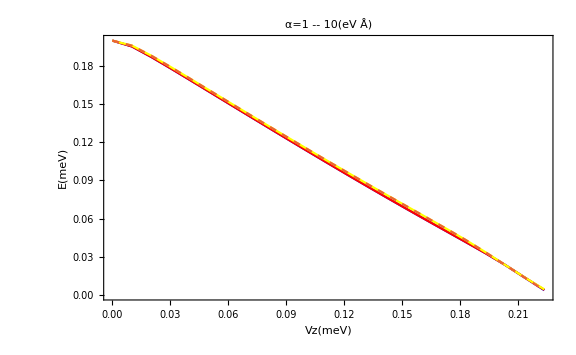
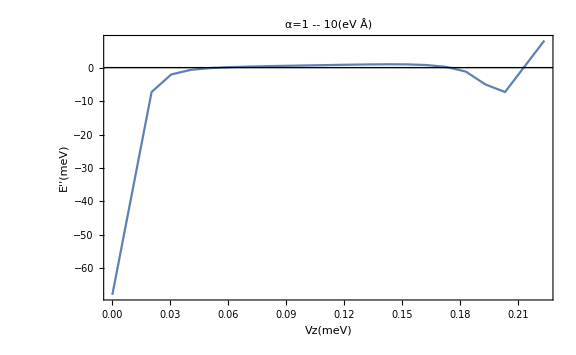

```mathematica
plot[1]
```

```mathematica
abs/.{t->25,Δ->.2,μ->.1,α->0.1}
```

0.223249

#### search max α

```mathematica
mu0p2=Table[maxα[.2,Δ],{Δ,0.1,1,.1}]
```

{2.03003,2.04956,2.07275,2.09473,2.10938,2.12402,2.13867,2.14844,2.14844,2.14844}

```mathematica
Dynamic[Δ]
```

```mathematica
Unset
```

```mathematica
maxα[.2,1.1]=.
```

```mathematica
maxα[.2,1.1]
```

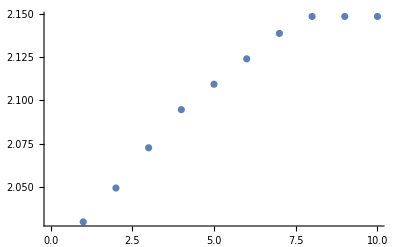

```mathematica
ListPlot[mu0p2]
```

```mathematica
maxα[.2,.5]
```

{2.5,-0.166852}

{1.25,0.480657}

{1.875,0.0891142}

{2.1875,-0.0309171}

$Aborted

```mathematica
maxα[.2,.2]
```

2.04956

```mathematica
maxα2[.2,.2]
```

2.88574

```mathematica
maxα2[.2,.2]/maxα[.2,.2]
```

1.40798

```mathematica
maxα2[.4,.2]/maxα[.4,.2]
```

1.40118

```mathematica
maxα3[.2,.2]/maxα[.2,.2]
```

1.72186

```mathematica
maxα3[.4,.2]/maxα[.4,.2]
```

1.71068

```mathematica
maxα4[.2,.2]/maxα[.2,.2]
```

1.9869

```mathematica
delta0p2=Table[maxα[μ,.2],{μ,0.02,0.6,0.02}];
```

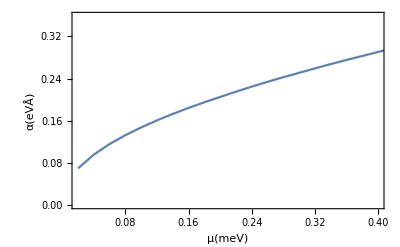

```mathematica
ListLinePlot[delta0p2/10,DataRange->{0.02,0.6},Frame->True,FrameLabel->{"μ(meV)","α(eVÅ)"},PlotRange->{{0.02,0.4},Automatic}]
```

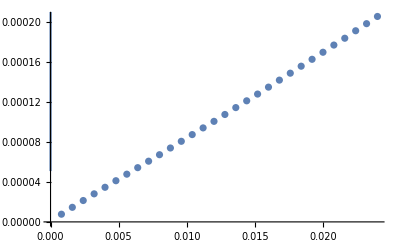

```mathematica
ListPlot[Transpose[{Range[.02,.6,.02]/25,(delta0p2/10/25)^2}],Epilog->{First@Plot[0.4596118210562973 √x,{x,0,0.6}]}]
```

```mathematica
0.008484636799114298*0.008484636799114298
```

0.0000719891

```mathematica
RootApproximant[0.008484636799114298,1]
```

4081/480987

```mathematica
10/11 √(η μ)/.{η->25,μ->0.4}
```

2.8748

```mathematica
maxα2[.2,.2]
```

2.03308

```mathematica
maxα2[.4,.2]
```

2.854

```mathematica
√(η μ)
```

```mathematica
ListPlot[delta0p2/10,DataRange->{0.02,0.6},Epilog->{First@Plot[0.4596118210562973 √x,{x,0,0.6}]}]
```

```mathematica
Fit[Transpose[{Range[.02,.6,.02],(delta0p2)^2}],{1,x},x]
```

-0.00463028+21.2116 x

```mathematica
0.4596118210562973*√(.001)
```

0.0145342

```mathematica
0.4596118210562973*√50
```

```mathematica
FindFit[Transpose[{Range[.02,.6,.02],delta0p2/10}],b x^n,{b,n},x]
```

{b→0.458883,n→0.4967}

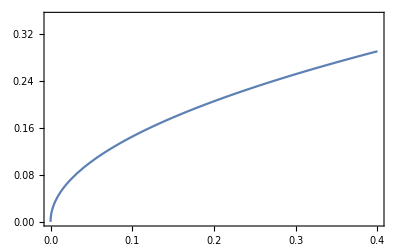

```mathematica
Plot[0.4596118210562973 √x,{x,0,0.4},PlotRange->{0,.35},Frame->True]
```

```mathematica
mapα=Table[maxα[μ,Δ],{μ,0.02,0.4,0.02},{Δ,.2,0.4,.02}];
```

$Aborted

```mathematica
Dynamic[{μ,Δ}]
```

#### μ=0.2,Δ=0.2

```mathematica
pl=Table[plot[α],{α,Union[Range[0.1,2.5,0.1],Range[2.,10.]]}];
```

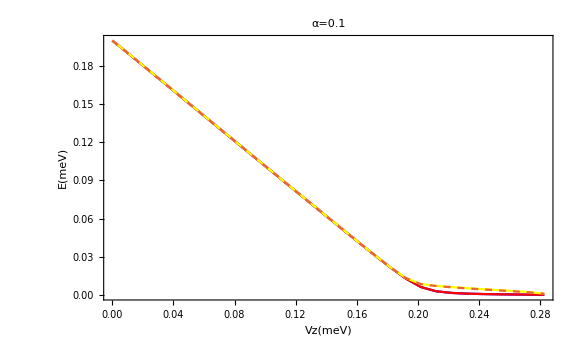
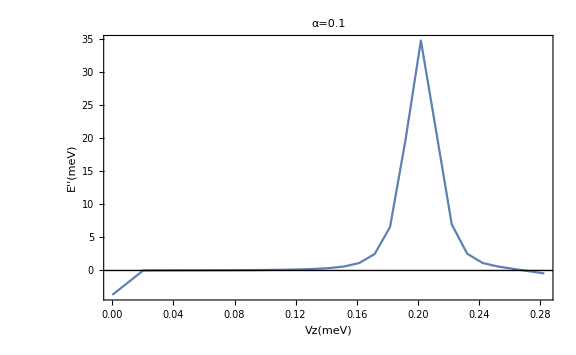
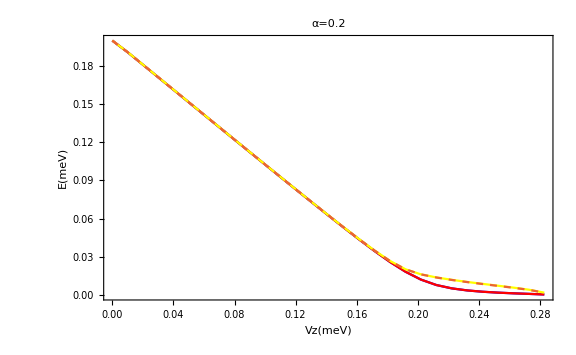
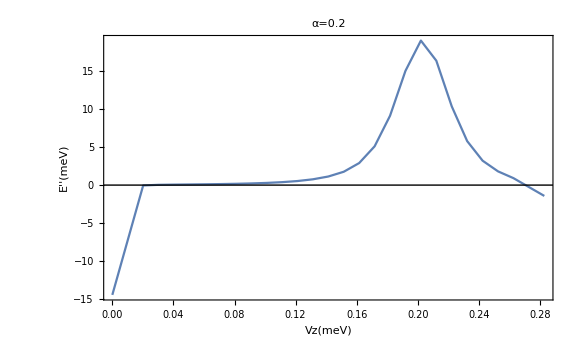
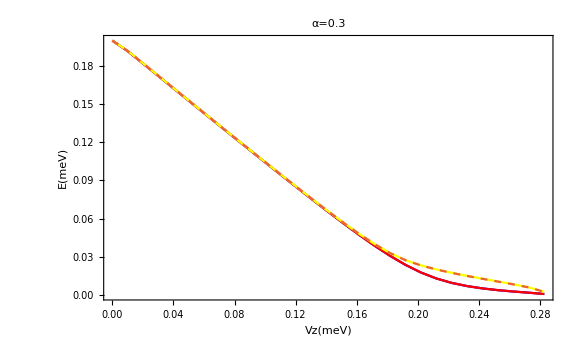
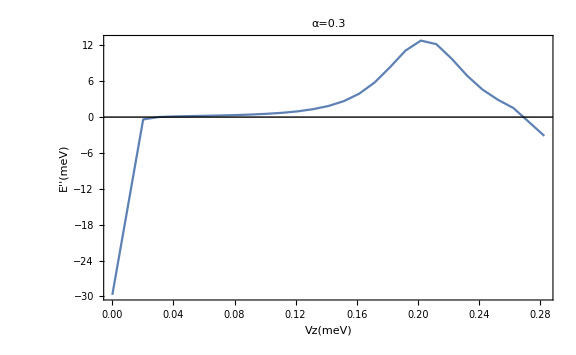
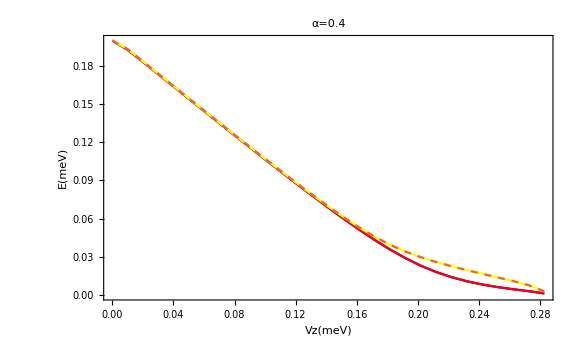
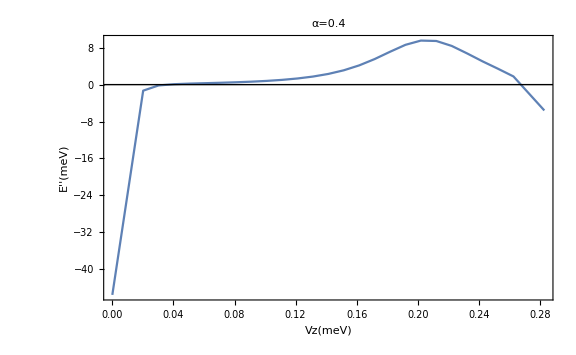
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid@pl
```

#### μ=0.1,Δ=0.2

```mathematica
pl2=Table[plot[α],{α,Union[Range[0.1,2.5,0.1],Range[2.,10.]]}];
```

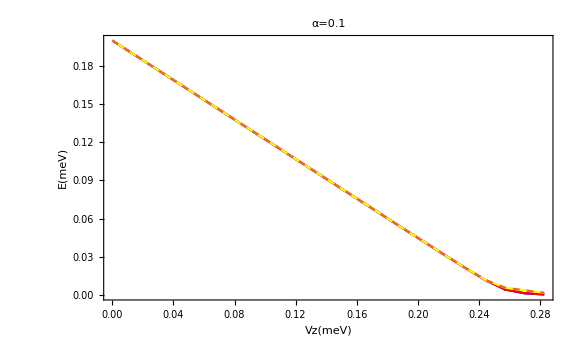
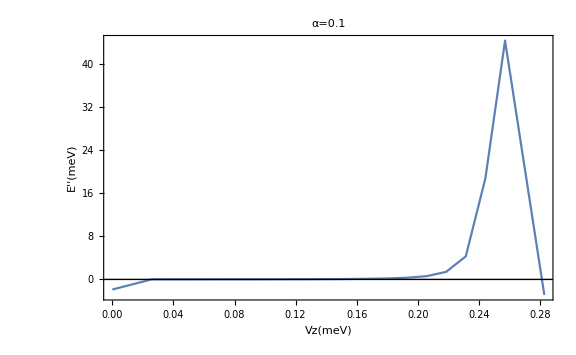
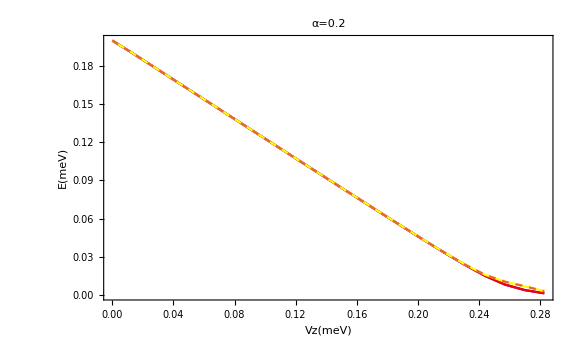
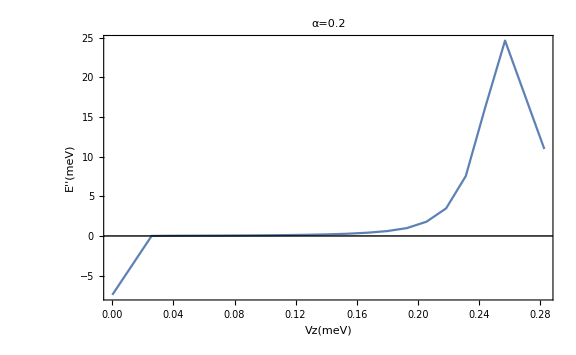
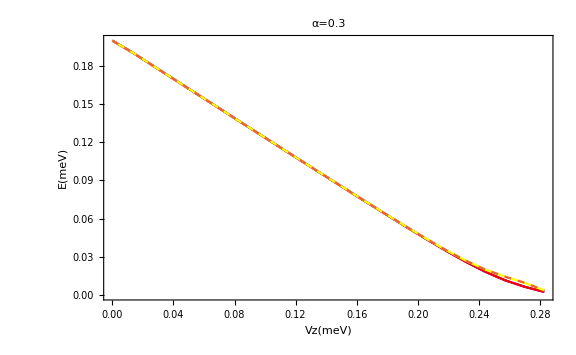
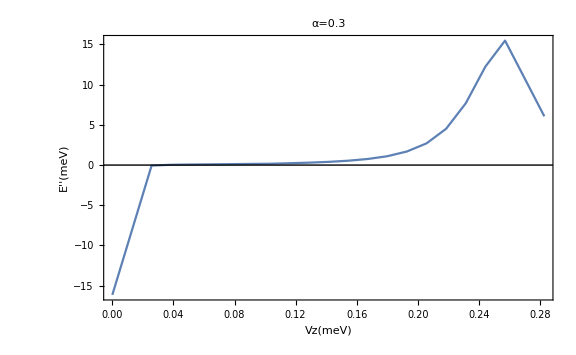
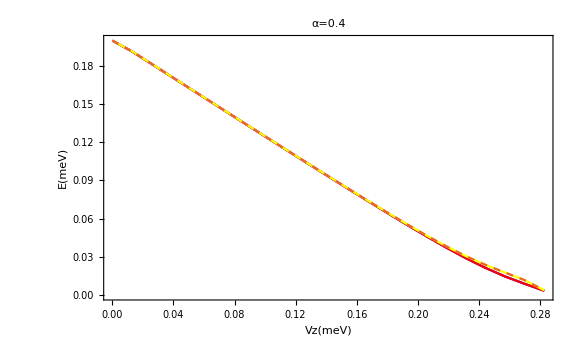
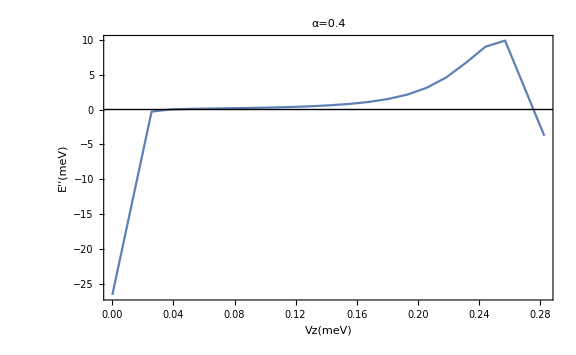
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid@pl2
```

#### μ=0.4,Δ=0.2

```mathematica
pl3=Table[plot[α],{α,Union[Range[0.1,2.5,0.1],Range[2.,10.]]}];
```

```mathematica
Grid@pl3
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

#### fixed alpha=1, varying μ,Vz

```mathematica
map=Table[plot2d[μ,.2,1],{μ,0,.4,0.005}];//AbsoluteTiming
```

{1369.04,Null}

```mathematica
PadRight[map,{Length@map,Length@map[[-1]]}]//Dimensions
```

{81,448}

```mathematica
Dynamic[μ]
```

```mathematica
ListDensityPlot[Transpose@Tanh@PadRight[map,{Length@map,Length@map[[-1]]}],PlotRange->{-10,10},PlotLegends->Automatic,DataRange->{{0,0.4},{0,√(.4^2+.2^2)}},FrameLabel->{"μ(meV)","Vz(meV)"},PlotRangePadding->None,ColorFunction->"TemperatureMap",Epilog->{ First@Plot[abs/.{α->1,t->25,Δ->0.2,μ->x},{x,0,0.4}]}]
```

-Graphics-

```mathematica
Export["mu0p3.png",Out[302]]
```

mu0p3.png

```mathematica
Plot[Tanh[x],{x,-10,10}]
```

-Graphics-

```mathematica
first deriv
```

deriv first

```mathematica
map=Table[plotg[μ,.2,1],{μ,0,.4,0.01}];//AbsoluteTiming
```

{1446.94,Null}

```mathematica
ListDensityPlot[Abs@PadRight[map,{Length@map,Length@map[[-1]]}],PlotRange->{-10,10},PlotLegends->Automatic,DataRange->{{0,√(.4^2+.2^2)},{0,0.4}},FrameLabel->{"V_Z(meV)","μ(meV)"},PlotRangePadding->None,ColorFunction->"TemperatureMap",PlotLabel->"g, α=0.1eV Å"]
```

-Graphics-

#### fixed alpha=2, varying μ,Vz

```mathematica
map2=Table[plot2d[μ,.2,2],{μ,0,.4,0.005}];//AbsoluteTiming
```

{1905.07,Null}

```mathematica
ListDensityPlot[Transpose@Tanh@PadRight[map2,{Length@map2,Length@map2[[-1]]}],PlotRange->{-10,10},PlotLegends->Automatic,DataRange->{{0,0.4},{0,√(.4^2+.2^2)}},PlotRangePadding->None,FrameLabel->{"μ(meV)","Vz(meV)"},ColorFunction->"TemperatureMap",Epilog->{ First@Plot[abs/.{α->2,t->25,Δ->0.2,μ->x},{x,0,0.4}]}]
```

-Graphics-

```mathematica
map2=Table[plotg[μ,.2,2],{μ,0,.4,0.01}];//AbsoluteTiming
```

{966.355,Null}

```mathematica
ListDensityPlot[Abs@PadRight[map2,{Length@map2,Length@map2[[-1]]}],PlotRange->{-10,10},PlotLegends->Automatic,DataRange->{{0,0.4},{0,√(.4^2+.2^2)}},PlotRangePadding->None,FrameLabel->{"V_Z(meV)","μ(meV)"},ColorFunction->"TemperatureMap",PlotLabel->"g, α=0.2eV Å"]
```

-Graphics-

#### fixed alpha=3, varying μ,Vz

```mathematica
map3=Table[plot2d[μ,.2,3],{μ,0,.4,0.005}];//AbsoluteTiming
```

{8131.44,Null}

```mathematica
ListDensityPlot[Transpose@Tanh@PadRight[map3,{Length@map3,Length@map3[[-1]]}],PlotRange->{-10,10},PlotLegends->Automatic,DataRange->{{0,0.4},{0,√(.4^2+.2^2)}},PlotRangePadding->None,FrameLabel->{"μ(meV)","Vz(meV)"},ColorFunction->"TemperatureMap",Epilog->{ First@Plot[abs/.{α->3,t->25,Δ->0.2,μ->x},{x,0,0.4}]}]
```

-Graphics-

```mathematica
map3=Table[plotg[μ,.2,3],{μ,0,.4,0.01}];//AbsoluteTiming
```

{733.781,Null}

```mathematica
ListDensityPlot[Abs@PadRight[map3,{Length@map3,Length@map3[[-1]]}],PlotRange->{-10,10},PlotLegends->Automatic,DataRange->{{0,0.4},{0,√(.4^2+.2^2)}},PlotRangePadding->None,FrameLabel->{"V_Z(meV)","μ(meV)"},ColorFunction->"TemperatureMap",PlotLabel->"g, α=0.3eV Å"]
```

-Graphics-

#### fixed alpha=5 varying μ,Vz

```mathematica
map5=Table[plot2d[μ,.2,5],{μ,0,.4,0.005}];//AbsoluteTiming
```

{4527.96,Null}

```mathematica
ListDensityPlot[Transpose@Tanh@PadRight[map5,{Length@map5,Length@map5[[-1]]}],PlotRange->{-10,10},PlotLegends->Automatic,DataRange->{{0,0.4},{0,√(.4^2+.2^2)}},PlotRangePadding->None,FrameLabel->{"μ(meV)","Vz(meV)"},ColorFunction->"TemperatureMap",Epilog->{ First@Plot[abs/.{α->5,t->25,Δ->0.2,μ->x},{x,0,0.4}]}]
```

-Graphics-

```mathematica
map5=Table[plotg[μ,.2,5],{μ,0,.4,0.01}];//AbsoluteTiming
```

{492.117,Null}

```mathematica
ListDensityPlot[Abs@PadRight[map5,{Length@map5,Length@map5[[-1]]}],PlotRange->{-10,10},PlotLegends->Automatic,DataRange->{{0,0.4},{0,√(.4^2+.2^2)}},PlotRangePadding->None,FrameLabel->{"V_Z(meV)","μ(meV)"},ColorFunction->"TemperatureMap",PlotLabel->"g, α=0.5eV Å"]
```

-Graphics-

```mathematica
?gap
```

Global`gap

gap[μ0_?NumberQ,Δ0_?NumberQ,B0_?NumberQ,α0_?NumberQ]:=Block[{Hf,ef,sl,findm,α=α0,η=25,μ=μ0,Δ=Δ0,V=B0,rt},Hf=H;rt=Solve[∂_k Hp1^2==0,k];sl=Select[rt⟦All,1,2⟧,#1∈ℝ&];Min[(Hp1/.k→#1&)/@sl]]

#### fixed alpha=.5, varying μ,Vz

```mathematica
map4=Table[plot2d[μ,.2,.5],{μ,0,.4,0.01}];//AbsoluteTiming
```

{2153.13,Null}

```mathematica
ListDensityPlot[Transpose@Tanh@PadRight[map4,{Length@map4,Length@map4[[-1]]}],PlotLegends->Automatic,DataRange->{{0,0.4},{0,√(.4^2+.2^2)}},PlotRangePadding->None,FrameLabel->{"μ(meV)","Vz(meV)"},ColorFunction->"TemperatureMap"]
```

-Graphics-

```mathematica
map4=Table[plotg[μ,.2,.5],{μ,0,.4,0.01}];//AbsoluteTiming
```

{2743.03,Null}

```mathematica
ListDensityPlot[Abs@PadRight[map4,{Length@map4,Length@map4[[-1]]}],PlotLegends->Automatic,DataRange->{{0,0.4},{0,√(.4^2+.2^2)}},PlotRangePadding->None,FrameLabel->{"V_Z(meV)","μ(meV)"},ColorFunction->"TemperatureMap",PlotLabel->"g, α=0.05eV Å"]
```

-Graphics-

#### fixed μ=0.2,varying vz,alpha

```mathematica
mapmu1=Table[plot2d[.2,.2,α],{α,0.5,5,0.1}];//AbsoluteTiming
```

{1623.58,Null}

```mathematica
ListDensityPlot[Transpose@Tanh@mapmu1,PlotLegends->Automatic,DataRange->{{0.05,.5},{0,√(.2^2+.2^2)}},PlotRangePadding->None,FrameLabel->{"α(eV Å)","Vz(meV)"},ColorFunction->"TemperatureMap"]
```

-Graphics-

```mathematica
ListDensityPlot[Transpose@Tanh@mapmu1,PlotLegends->Automatic,DataRange->{{0.5,5},{0,√(.2^2+.2^2)}},PlotRangePadding->None,FrameLabel->{"α(eV Å)","Vz(meV)"},ColorFunction->"TemperatureMap",Epilog->{ First@Plot[abs/.{t->25,Δ->.2,μ->.2},{α,0.5,5},PlotStyle->Yellow]}]
```

-Graphics-

```mathematica
mapmu1=Table[plotg[.2,.2,α],{α,0.1,1,0.1}];//AbsoluteTiming
```

{606.103,Null}

```mathematica
mapmu1=Table[plotg[.2,.2,α],{α,0.1,10,0.1}];//AbsoluteTiming
```

$Aborted

```mathematica
ListDensityPlot[Transpose@Abs@mapmu1,PlotLegends->Automatic,DataRange->{{0.01,1},{0,√(.2^2+.2^2)}},PlotRangePadding->None,FrameLabel->{"α(eV Å)","Vz(meV)"},ColorFunction->"TemperatureMap"]
```

#### fixed μ=0.4,varying vz,alpha

```mathematica
mapmu2=Table[plot2d[.4,.2,α],{α,0.5,5,0.1}];//AbsoluteTiming
```

{1653.79,Null}

```mathematica
ListDensityPlot[Transpose@Tanh@mapmu2,PlotLegends->Automatic,DataRange->{{0.05,.5},{0,√(.4^2+.2^2)}},PlotRangePadding->None,FrameLabel->{"α(eVÅ)","Vz(meV)"},ColorFunction->"TemperatureMap"]
```

-Graphics-

```mathematica
ListDensityPlot[Transpose@Tanh@mapmu2,PlotLegends->Automatic,DataRange->{{0.5,5},{0,√(.4^2+.2^2)}},PlotRangePadding->None,FrameLabel->{"α(eVÅ)","Vz(meV)"},ColorFunction->"TemperatureMap",Epilog->{ First@Plot[abs/.{t->25,Δ->.2,μ->.4},{α,0.5,5},PlotStyle->Yellow]}]
```

```mathematica
mapmu2=Table[plotg[.4,.2,α],{α,0.1,10,0.1}];//AbsoluteTiming
```

```mathematica
ListDensityPlot[Transpose@Abs@mapmu2,PlotLegends->Automatic,DataRange->{{0.01,1},{0,√(.4^2+.2^2)}},PlotRangePadding->None,FrameLabel->{"α(eV Å)","Vz(meV)"},ColorFunction->"TemperatureMap"]
```

```mathematica
ListLinePlot@Transpose@{Range[0,√(.4^2+.2^2),.001],plot2d[.4,.2,0.1]}
```

-Graphics-

```mathematica
ListLinePlot@Transpose@{Range[0,√(.4^2+.2^2),.001],plot2d[.4,.2,0.01]}
```

-Graphics-

```mathematica
abs/.{t->25,Δ->.2,μ->.4,α->0}
```

0.447214

#### fixed μ=0.1,varying vz,alpha

```mathematica
mapmu3=Table[plot2d[.1,.2,α],{α,0.5,5,0.1}];//AbsoluteTiming
```

{1520.57,Null}

```mathematica
ListDensityPlot[Transpose@Tanh@mapmu3,PlotLegends->Automatic,DataRange->{{0.05,.5},{0,√(.1^2+.2^2)}},PlotRangePadding->None,FrameLabel->{"α(eV Å)","Vz(meV)"},ColorFunction->"TemperatureMap"]
```

-Graphics-

```mathematica
Range[.05,5,.1][[10]]
```

0.95

```mathematica
ListDensityPlot[Transpose@Tanh@mapmu3,PlotLegends->Automatic,DataRange->{{0.5,5},{0,√(.1^2+.2^2)}},PlotRangePadding->None,FrameLabel->{"α(eV Å)","Vz(meV)"},ColorFunction->"TemperatureMap",Epilog->{ First@Plot[abs/.{t->25,Δ->.2,μ->.1},{α,0.5,5},PlotStyle->Yellow]}]
```

-Graphics-

#### fixed μ=0.3,varying vz,alpha

```mathematica
mapmu4=Table[plot2d[.3,.2,α],{α,0.5,5,0.1}];//AbsoluteTiming
```

{8232.18,Null}

```mathematica
ListDensityPlot[Transpose@Tanh@mapmu4,PlotLegends->Automatic,DataRange->{{0.05,.5},{0,√(.3^2+.2^2)}},PlotRangePadding->None,FrameLabel->{"α(eV Å)","Vz(meV)"},ColorFunction->"TemperatureMap"]
```

-Graphics-

```mathematica
Range[.05,5,.1][[10]]
```

0.95

```mathematica
ListDensityPlot[Transpose@Tanh@mapmu3,PlotLegends->Automatic,DataRange->{{0.5,5},{0,√(.1^2+.2^2)}},PlotRangePadding->None,FrameLabel->{"α(eV Å)","Vz(meV)"},ColorFunction->"TemperatureMap",Epilog->{ First@Plot[abs/.{t->25,Δ->.2,μ->.1},{α,0.5,5},PlotStyle->Yellow]}]
```

-Graphics-

### Fig1 pristine

```mathematica
α0p5=Block[{μ=.2,Δ=.2,α=.5,vzm,vzstep=0.001,p1,p2,data},vzm=.4;data=ParallelTable[{vz,First@Sort[Select[Chop@Re@Eigenvalues[SparseArray@Hc[1,μ,Δ,vz,α,3000],-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞,"Shift"->If[μ^2+Δ^2<vz^2,.5*gap[μ,Δ,vz,α],0]}],#>=0&]]},{vz,0,vzm,vzstep}]];
```

```mathematica
α2=Block[{μ=.2,Δ=.2,α=2,vzm,vzstep=0.001,p1,p2,data},vzm=.4;data=ParallelTable[{vz,First@Sort[Select[Chop@Re@Eigenvalues[SparseArray@Hc[1,μ,Δ,vz,α,3000],-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞,"Shift"->If[μ^2+Δ^2<vz^2,.5*gap[μ,Δ,vz,α],0]}],#>=0&]]},{vz,0,vzm,vzstep}]];
```

```mathematica
ListLinePlot[{α0p5,α2},Frame->True,FrameLabel->{Style["V_Z(meV)",Directive[Black,18]],Style["Energy(meV)",Directive[Black,18]]},FrameTicksStyle->Directive[Black,12],PlotLegends->Placed[{"α=0.05(eVÅ)","α=0.2 (eVÅ)"},Scaled[{.8,.8}]]]
```

-Graphics-

```mathematica
Plot[{Abs[Interpolation[α0p5]'[x]],Abs[Interpolation[α2]'[x]]},{x,0,.4},Frame->True,PlotRange->{0,1.},FrameLabel->{Style["V_Z(meV)",Directive[Black,18]],Style[Rotate["(∂E)/(∂ SubscriptBox[V, Z])",-90Degree],Directive[Black,18]]},FrameTicksStyle->Directive[Black,12],PlotLegends->Placed[{"α=0.05(eVÅ)","α=0.2 (eVÅ)"},Scaled[{.83,.8}]]]
```

-Graphics-

```mathematica
Plot[{Interpolation[α0p5]''[x],Interpolation[α2]''[x]},{x,0,.4},Frame->True,FrameLabel->{Style["V_Z(meV)",Directive[Black,18]],Style[Rotate["∂^2/(∂ SubsuperscriptBox[V, Z, 2])",-90Degree],Directive[Black,18]]},FrameTicksStyle->Directive[Black,12],PlotLegends->Placed[{"α=0.05(eVÅ)","α=0.2 (eVÅ)"},Scaled[{.84,.8}]]]
```

-Graphics-

```mathematica
μ0p1=Block[{μ=.1,Δ=.2,α=2,vzm,vzstep=0.001,p1,p2,data},vzm=.7;data=ParallelTable[{vz,Sort[Select[Chop@Re@Eigenvalues[SparseArray@Hc[1,μ,Δ,vz,α,3000],-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞,"Shift"->If[μ^2+Δ^2<vz^2,.5*gap[μ,Δ,vz,α],0]}],#>=0&]][[1]]},{vz,0,vzm,vzstep}]];
```

```mathematica
μ0p6=Block[{μ=.6,Δ=.2,α=2,vzm,vzstep=0.001,p1,p2,data},vzm=.7;data=ParallelTable[{vz,Sort[Select[Chop@Re@Eigenvalues[SparseArray@Hc[1,μ,Δ,vz,α,3000],-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞,"Shift"->If[μ^2+Δ^2<vz^2,.5*gap[μ,Δ,vz,α],0]}],#>=0&]][[1]]},{vz,0,vzm,vzstep}]];
```

```mathematica
ListLinePlot[{μ0p1,μ0p6},Frame->True,FrameLabel->{Style["V_Z(meV)",Directive[Black,18]],Style["Energy(meV)",Directive[Black,18]]},FrameTicksStyle->Directive[Black,12],PlotLegends->Placed[{"μ=0.1(meV)","μ=0.6(meV)"},Scaled[{.8,.8}]]]
```

-Graphics-

```mathematica
Plot[{Abs[Interpolation[μ0p1]'[x]],Abs[Interpolation[μ0p6]'[x]]},{x,0,.7},Frame->True,FrameLabel->{Style["V_Z(meV)",Directive[Black,18]],Style[Rotate["(∂E)/(∂ SubscriptBox[V, Z])",-90Degree],Directive[Black,18]]},FrameTicksStyle->Directive[Black,12],PlotLegends->Placed[{"μ=0.1(meV)","μ=0.6(meV)"},Scaled[{.6,.8}]]]
```

-Graphics-

```mathematica
Plot[{Interpolation[μ0p1]''[x],Interpolation[μ0p6]''[x]},{x,0,.7},Frame->True,FrameLabel->{Style["V_Z(meV)",Directive[Black,18]],Style[Rotate["∂^2/(∂ SubsuperscriptBox[V, Z, 2])",-90Degree],Directive[Black,18]]},FrameTicksStyle->Directive[Black,12],PlotLegends->Placed[{"μ=0.1(meV)","μ=0.6(meV)"},Scaled[{.6,.8}]]]
```

-Graphics-

### Fig2 SE Strong coupling

```mathematica
seα0p1=ParallelTable[{ii,iter[1,0.2,.3,ii,0.1,.3,3000,1]},{ii,0,1.2 √(.5^2+.1^2),0.01}];//AbsoluteTiming
```

{323.301,Null}

```mathematica
seα0p5=ParallelTable[{ii,iter[1,0.2,.3,ii,0.5,.3,3000,1]},{ii,0,1.2 √(.5^2+.1^2),0.003}];//AbsoluteTiming
```

{1056.43,Null}

```mathematica
seα5=ParallelTable[{ii,iter[1,0.2,.3,ii,5,.3,3000,1]},{ii,0,1.2 √(.5^2+.1^2),0.003}];//AbsoluteTiming
```

{930.059,Null}

```mathematica
ListLinePlot[{seα0p5,seα5},Frame->True,FrameLabel->{Style["V_Z(meV)",Directive[Black,18]],Style["Energy(meV)",Directive[Black,18]]},FrameTicksStyle->Directive[Black,12],PlotLegends->Placed[{"α=0.05(eVÅ)","α=0.5 (eVÅ)"},Scaled[{.8,.8}]]]
```

-Graphics-

```mathematica
Plot[{Abs[Interpolation[seα0p5]'[x]],Abs[Interpolation[seα5]'[x]]},{x,0,1.2 √(.5^2+.1^2)},Frame->True,FrameLabel->{Style["V_Z(meV)",Directive[Black,18]],Style[Rotate["(∂E)/(∂ SubscriptBox[V, Z])",-90Degree],Directive[Black,18]]},FrameTicksStyle->Directive[Black,12],PlotLegends->Placed[{"α=0.05(eVÅ)","α=0.5 (eVÅ)"},Scaled[{.8,.8}]]]
```

-Graphics-

```mathematica
Plot[{Interpolation[seα0p5]''[x],Interpolation[seα5]''[x]},{x,0,1.2 √(.5^2+.1^2)},PlotRange->{-6,10},Frame->True,FrameLabel->{Style["V_Z(meV)",Directive[Black,18]],Style[Rotate["∂^2/(∂ SubsuperscriptBox[V, Z, 2])",-90Degree],Directive[Black,18]]},FrameTicksStyle->Directive[Black,12],PlotLegends->Placed[{"α=0.05(eVÅ)","α=0.5 (eVÅ)"},Scaled[{.8,.8}]]]
```

-Graphics-

```mathematica
seμ0p1=ParallelTable[{ii,iter[1,0.1,.3,ii,2,.3,3000,1]},{ii,0,1.2 √(.6^2+.3^2),0.005}];//AbsoluteTiming
```

{1064.07,Null}

```mathematica
seμ0p6=ParallelTable[{ii,iter[1,0.6,.3,ii,2,.3,3000,1]},{ii,0,1.2 √(.6^2+.3^2),0.005}];//AbsoluteTiming
```

{958.641,Null}

```mathematica
ListLinePlot[{seμ0p1,seμ0p6},Frame->True,FrameLabel->{Style["V_Z(meV)",Directive[Black,18]],Style["Energy(meV)",Directive[Black,18]]},FrameTicksStyle->Directive[Black,12],PlotLegends->Placed[{"μ=0.1(meV)","μ=0.6(meV)"},Scaled[{.8,.8}]]]
```

-Graphics-

```mathematica
Plot[{Abs[Interpolation[seμ0p1]'[x]],Abs[Interpolation[seμ0p6]'[x]]},{x,0,1.2 √(.6^2+.3^2)},Frame->True,FrameLabel->{Style["V_Z(meV)",Directive[Black,18]],Style[Rotate["(∂E)/(∂ SubscriptBox[V, Z])",-90Degree],Directive[Black,18]]},FrameTicksStyle->Directive[Black,12],PlotLegends->Placed[{"μ=0.1(meV)","μ=0.6(meV)"},Scaled[{.6,.8}]]]
```

-Graphics-

```mathematica
Plot[{Interpolation[seμ0p1]''[x],Interpolation[seμ0p6]''[x]},{x,0,1.2 √(.6^2+.3^2)},Frame->True,FrameLabel->{Style["V_Z(meV)",Directive[Black,18]],Style[Rotate["∂^2/(∂ SubsuperscriptBox[V, Z, 2])",-90Degree],Directive[Black,18]]},FrameTicksStyle->Directive[Black,12],PlotLegends->Placed[{"μ=0.1(meV)","μ=0.6(meV)"},Scaled[{.6,.8}]]]
```

-Graphics-

### Plot of alpha_c (μ=0.02:0.02:1, deltalist=0.2:0.05:0.6)

```mathematica
alphac=Import["D:\\Nanowire\\Paper_curvature\\Figure\\alphac.dat"]
```

{{0.693359,0.959473,1.15723,1.32324,1.46851,1.59912,1.71936,1.83228,1.93726,2.03735,2.13379,2.22473,2.31323,2.39746,2.47925,2.55859,2.63672,2.71118,2.78442,2.85645,2.9248,2.99316,3.05908,3.125,3.18848,3.25195,3.31543,3.37402,3.43262,3.49121,3.5498,3.6084,3.66211,3.71582,3.76953,3.82813,3.87695,3.93066,3.98438,4.0332,4.08203,4.13086,4.17969,4.22852,4.27734,4.32617,4.375,4.41406,4.46289,4.51172},{0.703125,0.966797,1.16699,1.33301,1.47949,1.61133,1.73096,1.84326,1.94824,2.04834,2.14355,2.23511,2.32178,2.40723,2.48779,2.56714,2.64404,2.71851,2.79053,2.86133,2.93213,3.00049,3.06641,3.12988,3.19336,3.25684,3.31787,3.37891,3.4375,3.49609,3.55469,3.6084,3.66699,3.7207,3.77441,3.82813,3.88184,3.93555,3.98438,4.0332,4.08203,4.13574,4.18457,4.22852,4.27734,4.32617,4.375,4.42383,4.47266,4.51172},{0.703125,0.976563,1.17676,1.34277,1.48926,1.62109,1.74072,1.85303,1.95801,2.05811,2.15332,2.24487,2.33154,2.41577,2.49756,2.57568,2.65137,2.72705,2.79785,2.86865,2.93945,3.00537,3.07129,3.13721,3.20068,3.26172,3.3252,3.38379,3.44238,3.50098,3.55957,3.61328,3.67188,3.72559,3.7793,3.83301,3.88672,3.93555,3.98926,4.03809,4.0918,4.14063,4.18945,4.23828,4.28711,4.33105,4.375,4.42383,4.47266,4.51172},{0.703125,0.976563,1.18164,1.34766,1.49902,1.63086,1.75049,1.86279,1.96777,2.06787,2.16309,2.25342,2.34131,2.42432,2.50488,2.58423,2.66113,2.73438,2.80762,2.87598,2.94678,3.0127,3.07861,3.14453,3.20557,3.26904,3.33008,3.38867,3.44727,3.50586,3.56445,3.61816,3.67676,3.73047,3.78418,3.83789,3.88672,3.94043,3.99414,4.04297,4.0918,4.14063,4.18945,4.23828,4.28711,4.33594,4.38477,4.42383,4.47266,4.52148},{0.703125,0.976563,1.19141,1.35742,1.50391,1.63574,1.75781,1.87012,1.97754,2.07764,2.17285,2.26318,2.34863,2.43408,2.51465,2.59277,2.66846,2.7417,2.81494,2.88574,2.9541,3.02002,3.08594,3.14941,3.21289,3.27637,3.33496,3.396,3.45459,3.51074,3.56934,3.62305,3.68164,3.73535,3.78906,3.84277,3.8916,3.94531,3.99414,4.04785,4.09668,4.14551,4.19434,4.24316,4.28711,4.33594,4.38477,4.43359,4.47266,4.52148},{0.703125,0.976563,1.19141,1.36719,1.51367,1.64551,1.76758,1.87988,1.9873,2.08496,2.18018,2.27051,2.3584,2.44141,2.52197,2.6001,2.67578,2.75146,2.82227,2.89307,2.96143,3.02734,3.09326,3.15674,3.22021,3.28125,3.34229,3.40332,3.46191,3.51807,3.57422,3.63037,3.68652,3.74023,3.79395,3.84766,3.89648,3.9502,3.99902,4.05273,4.10156,4.15039,4.19922,4.24805,4.29688,4.34082,4.38477,4.43359,4.48242,4.52148},{0.703125,0.976563,1.19141,1.36719,1.51367,1.65039,1.77246,1.88477,1.99219,2.09473,2.1875,2.28027,2.36816,2.45117,2.5293,2.60742,2.68555,2.75879,2.82959,2.90039,2.96875,3.03467,3.10059,3.16406,3.22754,3.28857,3.34961,3.4082,3.4668,3.52539,3.5791,3.6377,3.69141,3.74512,3.79883,3.85254,3.90625,3.95508,4.00391,4.05762,4.10645,4.15527,4.2041,4.24805,4.29688,4.3457,4.39453,4.43848,4.48242,4.53125},{0.78125,1.01563,1.21094,1.36719,1.52344,1.66016,1.77734,1.89453,2.00195,2.09961,2.19727,2.28516,2.37305,2.45605,2.53906,2.61719,2.69043,2.76367,2.83691,2.90527,2.97363,3.04199,3.10547,3.17139,3.23242,3.2959,3.35449,3.41309,3.47168,3.53027,3.58887,3.64258,3.69629,3.75,3.80371,3.85742,3.91113,3.95996,4.01367,4.0625,4.11133,4.16016,4.20898,4.25781,4.30176,4.35059,4.39453,4.44336,4.4873,4.53125},{0.625,1.01563,1.21094,1.36719,1.52344,1.66016,1.78711,1.89453,2.00195,2.10938,2.20215,2.29492,2.38281,2.46582,2.54395,2.62207,2.7002,2.77344,2.84424,2.91504,2.9834,3.04688,3.11523,3.17871,3.24219,3.30078,3.36426,3.42285,3.48145,3.53516,3.59375,3.64746,3.70117,3.75977,3.80859,3.8623,3.91602,3.96484,4.01367,4.06738,4.11621,4.16504,4.21387,4.25781,4.30664,4.35547,4.4043,4.44336,4.49219,4.54102}}

```mathematica
valc=Import["D:\\Nanowire\\Paper_curvature\\Figure\\valc.dat"]
```

{{0.000473235,-0.000146043,0.000420908,-0.000435323,-0.000583978,-0.000864951,0.000265037,-0.000832234,0.000770271,0.000915211,-0.000966732,0.000100429,-0.000844901,0.000171348,0.000500961,0.000648439,-0.000576973,0.000150325,5.90228×10^-6,-0.000670522,0.000511698,0.000248006,0.000757542,0.000246092,0.000545234,0.0000848001,-0.000936283,0.000117599,0.00054291,0.000479983,0.0000420231,-0.00067979,0.000142243,0.000591196,0.000740158,-0.000801777,0.00036896,-0.000060301,-0.000604441,-0.0000901942,0.000234462,0.00040148,0.000437933,0.000366766,0.000207431,-0.0000235842,-0.000312312,0.000860332,0.000417765,-0.0000480058},{-0.000366429,0.00011917,0.0000803798,0.000407672,-0.000254741,-0.000858234,-2.26657×10^-6,-0.00046565,0.000586198,0.000319116,0.000196119,-0.000579602,0.000649143,-0.000912296,0.000451839,0.0000420644,-0.000140341,0.0000859381,0.000818681,0.000919298,-0.000480746,-0.000938857,-0.000546371,0.000599352,0.000730296,0.0000781579,0.000293129,-0.00011818,0.000270883,0.000137494,-0.000404653,0.00086077,-0.00036193,0.000129231,0.000287359,0.000176058,-0.00015137,-0.000650327,0.000131118,0.000660215,0.000977471,-0.0000902797,-0.000037462,0.000980247,0.000749872,0.00043737,0.0000585154,-0.000373241,-0.000846441,0.000286115},{0.000174252,-0.000626477,-0.000664488,-0.000185801,-0.000269698,-0.000410184,0.000773082,0.000705201,0.00066518,0.000542527,0.000393091,-0.000431602,0.000248913,0.0000338105,-0.000608685,0.0000364691,0.000793604,-0.000622597,0.000945731,0.000748482,-0.000848498,0.000476355,0.000558681,-0.000345739,-0.000329155,0.000510591,-0.000936156,5.66335×10^-6,0.00029469,0.0000565825,-0.000602,0.000679145,-0.00068828,-0.000206488,-0.0000723918,-0.000223382,-0.000606097,0.000471783,-0.000328334,0.00024887,-0.000818465,-0.000595176,-0.000537899,-0.000619778,-0.000817606,3.91076×10^-6,0.00064761,0.000116394,-0.000460548,0.00079403},{0.000307478,0.000297475,-0.0000254581,0.000893639,-0.000740371,-0.000722005,0.0000997688,0.000313881,0.000791084,0.000203431,-0.000245121,0.000311185,-0.000364815,0.000506592,0.000949307,0.000109226,-0.000583424,0.000153195,-0.000811383,0.000886422,-0.000804463,0.000224167,0.00012805,-0.000890763,0.000624404,-0.000309589,-0.000342801,0.000438599,0.000597282,0.000242826,-0.000529151,0.000694908,-0.000788592,-0.00035688,-0.000273335,-0.000479247,0.000906149,0.000181671,-0.000694869,-0.000102891,0.000253113,0.000407989,0.000392249,0.00023257,-0.0000477643,-0.000428462,-0.000891864,0.000806904,0.000128778,-0.000587167},{0.00032571,0.000582044,-0.000657035,-0.000133802,0.000253821,0.000742318,0.000623625,0.000873761,-0.0000584042,-0.00016871,-0.000576697,-0.00069354,0.000662199,-0.000496428,-0.000171291,0.0000140119,0.000265561,0.000750681,-0.000251831,-0.000723366,-0.000592122,0.000179168,-0.0000555877,0.000458175,0.000152189,-0.000841634,0.000453241,-0.000308179,-0.000224326,0.000632205,-0.000234589,0.000887114,-0.000678146,-0.0003215,-0.000303921,-0.000572233,0.000792966,8.92206×10^-6,0.0007861,-0.000354836,-0.0000127401,0.000126176,0.0000910675,-0.0000922582,0.000937714,0.000469857,-0.0000832051,-0.000706073,0.000894833,0.0000818078},{0.00030883,0.000654659,0.000115991,-0.000789908,-0.000565994,-0.000303633,-0.000387647,-0.0000642838,-0.000874104,0.000253973,0.000250089,0.000400774,-0.000351448,0.0000216948,0.000341522,0.000506559,0.000693438,-0.000551667,0.000118422,-0.000390313,-0.000384326,0.000192731,-0.000126191,0.000236594,-0.000143016,0.000219954,-0.0000416735,-0.000838696,-0.000833453,-0.0000775347,0.000202651,0.0000725585,-0.000407762,-0.000135733,-0.000188089,-0.000517834,0.000789064,-0.0000437655,0.000696384,-0.000494692,-0.000182543,-0.0000709688,-0.000132873,-0.000343958,-0.000682499,0.000199706,0.000893868,0.000186084,-0.000579912,0.000900636},{0.000280829,0.000626147,0.000437009,0.000102483,0.000599809,0.000145511,0.000257274,0.000558729,0.000317611,-0.000674152,0.000293759,-0.000490054,-0.000972063,-0.000788078,0.00038488,0.000570604,-0.000587337,-0.000287557,0.000261287,-0.000218341,-0.000269891,0.000174012,-0.0001789,0.0000736696,-0.000343781,-0.000085839,-0.000396999,5.30418×10^-7,-0.0000949781,-0.00062163,0.000701463,-0.00058135,-0.0000402652,0.000149738,0.0000327069,-0.000350547,-0.000962518,6.31446×10^-6,0.000693066,-0.000529926,-0.000257852,-0.000180555,-0.000273374,0.000932679,0.000515367,-9.45896×10^-6,-0.000625342,-0.0000575105,0.000362319,-0.00052755},{-0.000765966,-0.000722767,-0.000616559,0.000502924,-0.00013778,-0.000582277,0.000434202,-0.000260956,-0.000660403,0.000232218,-0.000640738,0.000433185,0.000266905,0.000603894,-0.00041672,-0.000568382,0.000572259,0.000879052,0.000203943,0.000972865,0.00091381,0.0000836735,0.000918403,-0.0000858675,0.000652906,-0.000329918,0.000462496,0.00075322,0.000592057,0.0000288028,-0.000887851,-0.0000790661,0.000365217,0.000483638,0.000313183,-0.000111154,-0.000756594,0.000132011,-0.000917878,-0.000479599,-0.000252202,-0.000211818,-0.000336357,-0.000605476,0.000392956,-0.00015435,0.000515253,-0.000243579,0.000162644,0.000439639},{0.000824802,-0.000476973,-0.000305341,0.000712239,0.000391106,0.000259405,-0.000277511,0.000896574,0.000938503,-0.000671372,0.000080363,-0.000504562,-0.000758265,-0.000410694,0.000579461,0.000577908,-0.000431153,-0.00044382,-1.78671×10^-6,-0.000339527,-0.00039056,0.000956591,-0.000405036,-0.000269108,-0.000676481,0.0004827,-0.000892647,-0.00065068,-0.000818775,0.000607246,-0.000297423,0.000398501,0.00076136,-0.000997344,0.000612765,0.000161763,-0.000502109,0.000303927,0.000865545,-0.000367651,-0.000185037,-0.000180639,-0.000334904,0.000782374,0.000325025,-0.000239461,-0.000896603,0.000888994,0.0000126192,-0.000918344}}

```mathematica
ListPlot[Transpose@{Range[.02,1,.02],#}]&/@alphac
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
fittedk=FindFit[Transpose@{Range[.02,1,.02],#},{k √μ},k,μ]&/@alphac
```

{{k→4.51556},{k→4.52218},{k→4.52989},{k→4.53683},{k→4.54395},{k→4.5519},{k→4.55957},{k→4.56777},{k→4.57467}}

```mathematica
ListPlot[Transpose@{Range[.02,1,.02],alphac[[1]]},Epilog->{First@Plot[fittedk[[1,1,2]] √x,{x,0,1}]},Frame->True,FrameLabel->{Style["μ(meV)",Directive[Black,18]],Style["α_c(eV nm)",Directive[Black,18]]}]
```

-Graphics-

### Legacy

```mathematica
tmp=Block[{μ=.6,Δ=.2,α=3,vzm,vzstep=0.001,p1,p2,data},vzm=.7;data=ParallelTable[{vz,Sort[Select[Chop@Re@Eigenvalues[SparseArray@Hc[1,μ,Δ,vz,α,3000],-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞,"Shift"->If[μ^2+Δ^2<vz^2,.5*gap[μ,Δ,vz,α],0]}],#>=0&]][[1]]},{vz,0,vzm,vzstep}]];
```

```mathematica
Plot[Interpolation[tmp]''[x],{x,0,0.7}]
```

-Graphics-

```mathematica
Plot[Interpolation[tmp,Method->"Spline",InterpolationOrder->3]''[x],{x,0,0.7}]
```

-Graphics-

```mathematica
ListLinePlot[tmp]
```

-Graphics-

```mathematica
fit=Fit[tmp,x^#&/@Range[0,4],x];
```

```mathematica
Plot[fit/.x->x0,{x0,0,.7},Epilog->{First@ListLinePlot[tmp,PlotStyle->Red]}]
```

-Graphics-

```mathematica
Plot[D[fit,{x,2}]/.x->xx,{xx,0,.7}]
```

-Graphics-

```mathematica
abs/.{t->25,α->3,Δ->.2,μ->.6}
```

0.617592

```mathematica
ListLinePlot[Most@((Differences@tmp[[All,2]]-RotateLeft@Differences@tmp[[All,2]])/0.001^2),DataRange->{0,0.7},PlotRange->{{0,abs/.{t->25,α->3,Δ->.2,μ->.6}},Automatic}]
```

-Graphics-

```mathematica
tmp2=Most@((Differences@tmp[[All,2]]-RotateLeft@Differences@tmp[[All,2]])/0.001^2)
```

{2.10067,2.09525,2.10077,2.1119,2.12527,2.13896,2.15196,2.1639,2.17475,2.18464,2.19378,2.20235,2.21053,2.21844,2.22617,2.23374,2.24119,2.24851,2.25567,2.26264,2.26939,2.27588,2.28206,2.28791,2.29337,2.29841,2.303,2.3071,2.31069,2.31373,2.3162,2.31808,2.31936,2.32002,2.32005,2.31944,2.3182,2.31632,2.31381,2.31069,2.30696,2.30264,2.29775,2.29231,2.28635,2.27989,2.27297,2.2656,2.25782,2.24965,2.24113,2.23228,2.22314,2.34483,2.59508,2.13085,2.12414,2.11731,2.11034,2.10325,2.09601,2.08863,2.08112,2.07345,2.06565,2.05769,2.04958,2.04133,2.03292,2.02437,2.01566,2.0068,1.99779,1.98864,1.97934,1.96989,1.9603,1.95056,1.94069,1.93069,1.92055,1.91028,1.89989,1.88938,1.87875,1.86801,1.85717,1.84622,1.83517,1.82403,1.8128,1.80149,1.7901,1.77864,1.76711,1.7862,1.75237,1.72605,1.71464,1.70321,1.69176,1.68028,1.66879,1.65727,1.64574,1.63417,1.62259,1.61098,1.59935,1.58769,1.57602,1.56432,1.55259,1.54085,1.52909,1.51731,1.50552,1.49371,1.48188,1.47005,1.4582,1.44634,1.43448,1.4247,1.41507,1.39788,1.38603,1.3742,1.36239,1.3506,1.33882,1.32706,1.31532,1.3036,1.2919,1.28022,1.26856,1.25691,1.24529,1.23369,1.22211,1.21055,1.19902,1.18751,1.17602,1.16456,1.15364,1.14268,1.13012,1.11877,1.10745,1.09617,1.08493,1.07372,1.06256,1.05142,1.04033,1.02928,1.01826,1.00729,0.996352,0.985456,0.974599,0.963783,0.953009,0.942275,0.931823,0.921112,0.910259,0.899693,0.889174,0.878701,0.868276,0.857897,0.847566,0.837282,0.827046,0.816859,0.806719,0.796628,0.786586,0.776593,0.766648,0.756753,0.747049,0.73711,0.72734,0.717643,0.707998,0.698404,0.688862,0.679373,0.669935,0.66055,0.651217,0.641936,0.632708,0.623533,0.61441,0.60534,0.596378,0.587361,0.578436,0.569576,0.560771,0.552019,0.543321,0.534676,0.526086,0.517549,0.509066,0.500637,0.492262,0.483941,0.475674,0.467489,0.459295,0.451187,0.443134,0.435135,0.427189,0.419298,0.411461,0.403677,0.395947,0.388271,0.380648,0.373079,0.365567,0.358112,0.350689,0.343333,0.33603,0.32878,0.321583,0.314439,0.307348,0.300311,0.293325,0.286393,0.279513,0.272687,0.265915,0.259185,0.252513,0.245893,0.239326,0.23281,0.226345,0.219933,0.213571,0.207261,0.201002,0.194794,0.188641,0.182529,0.176473,0.170467,0.164511,0.158606,0.152751,0.146945,0.14119,0.135483,0.129827,0.124221,0.118663,0.113152,0.107691,0.102279,0.0969163,0.0916016,0.0863351,0.0811168,0.0759465,0.070824,0.0657497,0.0607232,0.0557415,0.0508086,0.0459227,0.0410838,0.0362917,0.0315462,0.0268472,0.0221944,0.0175879,0.0130282,0.00851292,0.0040433,-0.000380235,-0.00475837,-0.00909122,-0.0133789,-0.0176217,-0.0218196,-0.0259728,-0.0300811,-0.0341454,-0.0381661,-0.0421422,-0.0460743,-0.0499625,-0.0538071,-0.0576081,-0.0613657,-0.0650801,-0.0687508,-0.0723793,-0.075965,-0.0795077,-0.0830078,-0.0864653,-0.0898806,-0.0932536,-0.0965846,-0.0998734,-0.10312,-0.106326,-0.10949,-0.112612,-0.115693,-0.118733,-0.121732,-0.124689,-0.127606,-0.130482,-0.133317,-0.136112,-0.138866,-0.14158,-0.144254,-0.146887,-0.14948,-0.152033,-0.154547,-0.15702,-0.159454,-0.161849,-0.164203,-0.166518,-0.168794,-0.171031,-0.173228,-0.175386,-0.177506,-0.179586,-0.181627,-0.183629,-0.185593,-0.187517,-0.189403,-0.19125,-0.193059,-0.194829,-0.196561,-0.198254,-0.199909,-0.201526,-0.203104,-0.204643,-0.206145,-0.207608,-0.209033,-0.21042,-0.211768,-0.213078,-0.21435,-0.215584,-0.21678,-0.217938,-0.219057,-0.220138,-0.221181,-0.222186,-0.223152,-0.224081,-0.224971,-0.225822,-0.226635,-0.22741,-0.228146,-0.228844,-0.229503,-0.230124,-0.230706,-0.231249,-0.231754,-0.232219,-0.232646,-0.233033,-0.233381,-0.23369,-0.23396,-0.23419,-0.234381,-0.234531,-0.234642,-0.234713,-0.234744,-0.234735,-0.234685,-0.234594,-0.234463,-0.234291,-0.234078,-0.233823,-0.233527,-0.233189,-0.23281,-0.232388,-0.231924,-0.231417,-0.230867,-0.230275,-0.229639,-0.228959,-0.228235,-0.227468,-0.226655,-0.225798,-0.224896,-0.223948,-0.222954,-0.221915,-0.220828,-0.219695,-0.218515,-0.217286,-0.21601,-0.214685,-0.213311,-0.211887,-0.210414,-0.20889,-0.207315,-0.205689,-0.204011,-0.20228,-0.200496,-0.198658,-0.196766,-0.194819,-0.192817,-0.190758,-0.188642,-0.186469,-0.184238,-0.181947,-0.179596,-0.177185,-0.174712,-0.172177,-0.169579,-0.166917,-0.164189,-0.161396,-0.158536,-0.155608,-0.152611,-0.149543,-0.146405,-0.143194,-0.13991,-0.136551,-0.133116,-0.129604,-0.126013,-0.122342,-0.11859,-0.114755,-0.110835,-0.10683,-0.102737,-0.0985546,-0.0942815,-0.0899158,-0.0854555,-0.0808987,-0.0762436,-0.0714881,-0.0666302,-0.0616676,-0.0565981,-0.0514195,-0.0461293,-0.0407252,-0.0352045,-0.0295646,-0.0238028,-0.0179163,-0.0119021,-0.00575728,0.000521388,0.00693705,0.0134931,0.0201931,0.0270405,0.0340392,0.0411929,0.0485058,0.055982,0.0636258,0.0714416,0.0794343,0.0876085,0.0959694,0.104522,0.113272,0.122225,0.131387,0.140763,0.150361,0.160187,0.170248,0.18055,0.191102,0.201911,0.212985,0.224333,0.235963,0.247886,0.260109,0.272644,0.285501,0.298691,0.312226,0.326116,0.340376,0.355018,0.370055,0.385503,0.401377,0.417691,0.434464,0.451712,0.469454,0.487709,0.506498,0.525841,0.545762,0.566284,0.587432,0.609232,0.631713,0.654903,0.678833,0.703537,0.729048,0.755405,0.782645,0.81081,0.839943,0.870092,0.901305,0.933635,0.967137,1.00187,1.0379,1.0753,1.11413,1.15447,1.19641,1.24004,1.28544,1.33273,1.38201,1.4334,1.48703,1.54303,1.60156,1.66277,1.72684,1.79395,1.86431,1.93815,2.0157,2.09724,2.18304,2.27343,2.36875,2.46939,2.57576,2.68834,2.80763,2.9342,3.06869,3.2118,3.36432,3.52713,3.70122,3.88771,4.08786,4.30309,4.53505,4.78558,5.05683,5.35126,5.67171,6.0215,6.40449,6.82526,7.28917,7.80266,8.37341,9.01071,9.72588,10.5328,11.4489,12.4957,13.7007,15.0996,16.7386,18.6794,21.0055,23.8329,27.3263,31.7274,37.4034,44.938,55.4804,73.4555,54.567,9.89428,0.452473,-1.93882,-3.91705,-7.06576,-13.6279,-30.3729,-83.9291,-260.653,-408.939,-157.426,-20.0142,-1.81736,-0.160189,-0.0147113,-0.00141286,-0.000188876,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Length@Most@Range[0,0.7,0.001]
```

700

```mathematica
Length@tmp2
```

699

```mathematica
ListPlot@Transpose@{Drop[Range[0,0.7,0.001],2],tmp2}
```

-Graphics-

```mathematica
tmp3=Select[Transpose@{Drop[Range[0,0.7,0.001],2],-tmp2},#[[1]]<abs/.{t->25,α->3,Δ->.2,μ->.6}&];
```

```mathematica
fit2=Fit[tmp3,x^#&/@Range[0,20],x]
```

1.88629+92.0713 x-11264.3 x^2+722552. x^3-2.62442×10^7 x^4+5.93601×10^8 x^5-8.99396×10^9 x^6+9.57724×10^10 x^7-7.38805×10^11 x^8+4.19876×10^12 x^9-1.76503×10^13 x^10+5.41748×10^13 x^11-1.15838×10^14 x^12+1.46357×10^14 x^13-5.7014×10^12 x^14-4.10474×10^14 x^15+9.3845×10^14 x^16-1.16536×10^15 x^17+8.8326×10^14 x^18-3.85528×10^14 x^19+7.48092×10^13 x^20

```mathematica
Plot[fit2/.x->x0,{x0,0,.7}]
```

-Graphics-

```mathematica
ListPlot[tmp3]
```

-Graphics-

```mathematica
FindPeaks[tmp3[[All,2]],1000]
```

{{400,0.234744}}

```mathematica
alphac=Import["D:\\CMTC\\fitexpSA\\matlab\\alphac.dat"]
```

{{2.03125,2.1875,2.5,2.8125,3.75,3.125,3.75,4.6875,4.375,0.,0.,0.},{2.03125,2.26563,2.5,2.65625,2.8125,3.125,3.125,3.125,3.75,0.,0.,0.},{2.03125,2.26563,2.5,2.65625,2.8125,3.125,3.125,3.125,3.75,0.,0.,0.},{2.03125,2.26563,2.5,2.65625,2.8125,3.125,3.125,3.4375,3.4375,0.,0.,0.},{2.03125,2.34375,2.5,2.65625,2.8125,3.125,3.125,3.4375,3.4375,0.,0.,0.},{2.03125,2.34375,2.5,2.65625,2.8125,3.125,3.125,3.4375,3.4375,0.,0.,0.},{2.03125,2.34375,2.5,2.65625,2.8125,3.125,3.125,3.4375,3.4375,0.,0.,0.},{2.1875,2.1875,2.5,2.8125,2.8125,3.125,3.125,3.4375,3.4375,0.,0.,0.},{2.1875,2.1875,2.5,2.8125,2.8125,3.125,3.125,3.4375,3.4375,0.,0.,0.},{1.875,2.5,2.5,2.8125,2.8125,3.125,3.125,3.4375,3.4375,0.,0.,0.},{1.875,2.5,2.5,2.8125,2.8125,3.125,3.125,3.4375,3.75,0.,0.,0.},{1.875,2.5,2.5,2.5,3.125,3.125,3.125,3.4375,3.75,0.,0.,0.}}

```mathematica
ListPlot[alphac[[1]]]
```

-Graphics-